# Path Integrals using Monte Carlo approximation

## Python

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import["PIMC-sim.py"]
```

Finished in 33.57 seconds

======Harmonic Oscillator========

Acceptance number/rate(%): 124349 / 24.92 %

Vacuum energy using PI: 0.448

Vacuum energy mean using PI: 0.451

1st Excitation Energy using PI: 1.42

Theoretical vacuum energy: 0.484

Theoretical 1st excitation energy: 1.453

Percentage error: 7.59 %

Standar Deviation: 0.0035027618949209343

Standrd Error: [0.002022320522939765]

% std error: [0.44839711]

## Mathematica

## Symbolic derivation

```mathematica
freeVelocity[i_]:=With[{
		symbol1 = x[i],
		symbol2 = x[i+1]
	},
	(symbol2-symbol1)/Δt
]
```

```mathematica
K[v_,i_] := (m*v[i]^2)/2;

K[v_][i_]:= K[v,i];
```

```mathematica
V[w_,i_] := (m*(w*x[i])^2)/2;

V[w_][i_] := V[w,i];
V[0][i_] := 0;
```

```mathematica
L[K_,V_,i_]:= K[i]-V[i];

L[K_,V_][i_]:=L[K,V,i];
```

```mathematica
S[L_, i_]:=With[{
		t1symbol = t[i],
		t2symbol = t[i+1],
		x1symbol = x[i],
		x2symbol = x[i+1]
	},
	Integrate[
		L[i],
		{t,t1symbol,t2symbol}
	]
	/.(t2symbol-t1symbol) -> Δt
	/.(0[_]) -> 0
];
S[L_][i_] := S[L,i];
```

```mathematica
S[ L[K[freeVelocity],0] ][0]
```

(m (-x[0]+x[1])^2)/(2 Δt)

## Monte Carlo approximation

```mathematica
Quit
```

### Math Constants

ClearAll[μ,m,ω];

m1 = 1;
m2 = 1;

m = 1(*(m1 * m2)/(m1+m2)*);



k = 1;

ω[ϵ_] := k/(√m)(1 - (k^2 ϵ^2)/(8 m));

t[ϵ_,i_] := i*ϵ;

### Symbolic functions

ClearAll["harmonic*", "action*"];

harmonicVelocity[x_,ϵ_, i_,j_] := (x[[j]]-x[[i]])/ϵ;

harmonicVelocity[x_,ϵ_,i_] := (x[[i+1]]-x[[i]])/ϵ;

harmonicKinetic[x_, i_, j_] := (m*harmonicVelocity[x, i, j]^2)/2;

harmonicKinetic[x_, i_] := (m*harmonicVelocity[x, i]^2)/2;

harmonicPotential[x_,i_] :=(k^2*x[[i]]^2)/2;

action[K_,V_][x_, i_] := action[K, V, x, i];
action[K_,V_,x_,i_]  := (
	ϵ*V[x, i]+K[x, i]+K[x, i-1]
);

action2[K_,V_][x_, i_] := action2[K, V, x, i];
action2[K_,V_,x_,i_]  := (
	ϵ*V[x, i]+K[x, i]
);

action3[K_,V_][x_, i_] := action3[K, V, x, i];
action3[x_,V_, ϵ_, i_]  := (
	ϵ*V[x, i]+x[[i]]*(x[[i]]-x[[i+1]]-x[[i-1]])/ϵ
);


pathEnergy[K_,V_][x_,i_] := pathEnergy[K, V, x, i];
pathEnergy[K_, V_, x_, i_] := Module[{},
	Plus @@
	Table[
		K[x, i+1, j]+ V[x, i],
		{j, Length[x]-1}
	]
];

### Compiled functions

harmonicVelocityIndexedCompiled = FunctionCompile[
	Function[{
			Typed[x, TypeSpecifier["PackedArray"]["Real64",1]],
			Typed[ϵ, "Real64"],
			Typed[i, "MachineInteger"],
			Typed[j, "MachineInteger"]
			
		},
		(x[[j]]-x[[i]])/ϵ
	]
] ;
harmonicVelocityCompiled = FunctionCompile[
	Function[{
			Typed[x, TypeSpecifier["PackedArray"]["Real64",1]],
			Typed[ϵ, "Real64"],
			Typed[i, "MachineInteger"]
		},
		(x[[i+1]]-x[[i]])/ϵ
	]
];

harmonicKineticCompiled = FunctionCompile[
	Function[{
			Typed[m, "Real64"],
			Typed[v, "Real64"]
		},
		(m*v^2)/2
	]
];

harmonicPotentialCompiled= FunctionCompile[
	Function[{
			Typed[x, TypeSpecifier["PackedArray"]["Real64",1]],
			Typed[k, "Real64"],
			Typed[i, "MachineInteger"]
		},
		(k^2*x[[i]]^2)/2
	]
];

action1Compiled = FunctionCompile[
	Function[{
			Typed[K1, "Real64"],
			Typed[K2, "Real64"],
			Typed[V, "Real64"],
			Typed[ϵ, "Real64"]
		},
		ϵ*(V+K1+K2)
	]
];
action2Compiled = FunctionCompile[
	Function[{
			Typed[K, "Real64"],
			Typed[V, "Real64"],
			Typed[ϵ, "Real64"]
		},
		ϵ*(V+K)
	]
];
action3Compiled = FunctionCompile[
	Function[{
			Typed[x, TypeSpecifier["PackedArray"]["Real64",1]],
			Typed[V, "Real64"],
			Typed[ϵ, "Real64"],
			Typed[i, "MachineInteger"]
		},
		(ϵ*V+x[[i]]*(x⟦i⟧-x⟦Mod[i+1,Length[x],1]⟧-x⟦Mod[i-1,Length[x],1]⟧)/ϵ)
	]
];

actionCompiled[S_, K_, V_, v_, m_, k_][x_,ϵ_, i_] :=
	S[
		K[m,v[x,ϵ,i]],
		K[m,v[x,ϵ,i-1]],
		V[x,k,i],
		ϵ
	];

actionCompiled2[S_, K_, V_, v_, m_, k_][x_,ϵ_, i_] :=
	S[
		K[m,v[x,ϵ,i]],
		V[x,k,i],
		ϵ
	];

actionCompiled3[S_, K_, V_, v_, k_][x_,ϵ_, i_] :=
	S[
		x,
		V[x,k,i],
		ϵ,
		i
	];

pathEnergyCompiled[K_,V_,v_,m_,k_][x_,ϵ_,i_]:=
	Plus @@
	Table[
		K[m,v[x,ϵ,i,j]]+ V[x, k,i],
		{j, Length[x]-1}
	];

pathEnrgy2Compiled=FunctionCompile[
	Function[{
			Typed[x, TypeSpecifier["PackedArray"]["Real64",1]],
			Typed[K, {"MachineInteger"}->"Real64"](*i , j*),
			Typed[V, "Real64"]
			
		},
		Module[{
			tally = 0
		},
		Table[
			tally += K[j]+ V,
			{j, Length[x]-1}
			]
		]
	]
];

harmonicPathEnergyCompiled [K_,V_,v_, m_,k_][x_,ϵ_,i_] :=pathEnrgy2Compiled[x, K[m,v[x, ϵ, i, #]]&, V[x, k,i]];

```mathematica
harmonicPathEnergyCompiled[
	harmonicKineticCompiled,
	harmonicPotentialCompiled,
	harmonicVelocityIndexedCompiled,
	m,
	k
][{0,0,0,0},0.1,2]
```

Failure[…]

```mathematica
pathEnergyCompiled[
	harmonicKineticCompiled,
	harmonicPotentialCompiled,
	harmonicVelocityIndexedCompiled,
	k
][{0,0,0,0},0.1,2]
```

0.

```mathematica
actionCompiled3[ action3Compiled, harmonicKineticCompiled, harmonicPotentialCompiled, harmonicVelocityCompiled, k ][{0,0,1,0,0}, 0.1, 2]
```

0.

### updatePath

#### test

```mathematica
Clear[tst];
```

```mathematica
dec = FunctionDeclaration[
	tst,
	Typed[{TypeSpecifier["NumericArray"]["Real64",1], "Real64", "MachineInteger"} -> "Real64"]@Function[{x,e,i},
		actionCompiled3[ action3Compiled, harmonicKineticCompiled, harmonicPotentialCompiled, harmonicVelocityCompiled, k ][x,e,i]
	]
]
```

FunctionDeclaration[tst,Typed[{TypeSpecifier[NumericArray][Real64,1],Real64,MachineInteger}→Real64][Function[{x,e,i},actionCompiled3[action3Compiled,harmonicKineticCompiled,harmonicPotentialCompiled,harmonicVelocityCompiled,k][x,e,i]]]]

```mathematica
updateVariablesCompiled = FunctionCompile[dec,
	Function[
		{
			(*Typed[S, {TypeSpecifier["NumericArray"]["Real64",1], "Real64", "MachineInteger"} -> "Real64"],*)
			Typed[x, TypeSpecifier["NumericArray"]["Real64",1]],
			Typed[dt,  "Real64"],
			Typed[g,   "MachineInteger"],
			Typed[rand1, "Real64"],
			Typed[rand2, "Real64"],
			Typed[len, "MachineInteger"]
		},
			Table[
				Block[{
						S = tst,
						rand,
						xOld,
						xNew,
						SOld,
						dS,
						probability,
						acceptanceNumber = g,
						path = x
					},
					rand = rand1;
					xOld = path[[i]];
					xNew = path[[i]] + rand2;
					SOld = S[path, dt, i];
					path[[i]] = xNew;
					dS = S[path, dt, i] - SOld;
					probability = N[ Exp[-dS] ];
					
					If[dS > 0,
						If[probability < rand,
							path[[i]] = xOld,
							acceptanceNumber += 1
						],
						acceptanceNumber += 1
					];
				
					{
						path,
						acceptanceNumber
					}
				],
				{i, 2, len-1}
			]
	]
]
```

Failure[…]

```mathematica
<<Developer`
```

```mathematica
PackedArrayQ[Append[0.]@ConstantArray[ 0. , {20}]]
```

True

```mathematica
ToPackedArray[ConstantArray[ 0. , {20}]]//FullForm
```

List[0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.]

ClearAll[updatePath];

Options[updatePath]={
	"SelectionThreshold"-> 3,
	"ComputePathEnergy" -> False
};
updatePath[S_, E_, opts:OptionsPattern[]][x_, t_] := updatePath[x, S, E, {t}, opts];
updatePath[x_List, S_, E_, {t0_Integer:0,tf_Integer}, OptionsPattern[]] := 
	Block[{
			xOld,xNew,iterations,Δt,energies,
			rand,SOld,dS,probability,isThermalised,
			path = x,
			acceptanceNumber = 0,
			eps = OptionValue["SelectionThreshold"],
			tStart = t0,
			tEnd = tf,
			computeEnergy = OptionValue["ComputePathEnergy"],
			pathLength = Length[x]
		},
		energies = ConstantArray[ 0. , {pathLength}];
		Δt = N[(tf-t0)/pathLength];
		Table[
			rand = RandomReal[{0,1}](*RandomVariate[UniformDistribution[{0,1}]]*);
			xOld = path[[i]];
			xNew = path[[i]] + RandomReal[{-eps, eps}](*RandomVariate[UniformDistribution[{-eps,eps}]]*);
			SOld = S[path, Δt, i];
			path[[i]] = xNew;
			dS = S[path, Δt, i] - SOld;
			probability = N[Exp[-dS]];
			
			If[dS > 0,
				If[probability < rand,
					path[[i]] = xOld,
					acceptanceNumber += 1
				],
				acceptanceNumber += 1
			];
			
			If[computeEnergy, energies[[i]] = E[path, Δt, i]];
			,
			{i, 2, pathLength-1}
		];

		{
			path,
			If[computeEnergy, energies, Nothing],
			{
				acceptanceNumber,
				acceptanceNumber/(pathLength-2)
			}
		}
	];

```mathematica
updatePath[
	actionCompiled3[ action3Compiled, harmonicKineticCompiled, harmonicPotentialCompiled, harmonicVelocityCompiled, k ],
	pathEnergyCompiled[  harmonicKineticCompiled,harmonicPotentialCompiled,harmonicVelocityIndexedCompiled,k ]
][{1,2,3,4},4]
```

{{1,0.164092,3,4},{1,1/2}}

### NPathIntegral

Clear[NPathIntegral];

Options[NPathIntegral]={
	"LatticePoints" -> 500,
	"ThermilisationLength" -> 500,
	"ComputePathEnergy"->False,
	"Iterations" -> 1000,
	"SelectionThreshold" -> 3,
	"OptimalAcceptanceRate" -> 0.8,
	"OptimalAcceptanceVariant" -> 0.01,
	"NumberOfPaths" -> 3,
	"OptimiseAcceptance" -> True
};
NPathIntegral[S_, En_, x0_, t_, opts:OptionsPattern[]] := NPathIntegral[S, En, {x0}, {t}, opts];
NPathIntegral[S_, En_, {x0_:0,xf_}, {t0_:0, tf_}, OptionsPattern[]] :=
	Block[{path,accNo,progress1,progress2,progress3,energies,pathsSquared,pathSquared,
			timing1,timing2,Δt,Ne0,e0,Ne1,e1,paths,getRandomAcceptanceVariant,
			clock = Dynamic[Clock[]],
			acceptanceNumbers = {},
			optimise = OptionValue["OptimiseAcceptance"],
			noOfPaths = OptionValue["NumberOfPaths"],
			optVar = OptionValue["OptimalAcceptanceVariant"],
			optimalAcceptance = OptionValue["OptimalAcceptanceRate"],
			computeEnergy = OptionValue["ComputePathEnergy"],
			eps = OptionValue["SelectionThreshold"],
			iterations = OptionValue["Iterations"],
			latticeSpacing = OptionValue["LatticePoints"],
			
			x2={},e0tmp={}
			
		},
		getRandomAcceptanceVariant = RandomVariate[UniformDistribution[{-optVar/3, optVar}]]&;
		Δt = N[(tf - t0)/latticeSpacing];
		path = 
			Append[
				Prepend[
					x0
					][
					ConstantArray[ 0. , {latticeSpacing-2} ]
					],
					xf
			];
			
		PrintTemporary[ProgressIndicator[Dynamic[progress1/OptionValue["ThermilisationLength"]]]," Thermalising"];
		
		timing1 = 
			First[
				AbsoluteTiming[
				Monitor[
				Table[
					progress1 = j;
					
					{path,accNo} = updatePath[S, En, "SelectionThreshold" -> eps][path,tf];
					
					If[optimise,
						If[ optimalAcceptance - 0.1 < accNo[[2]] < optimalAcceptance + 0.1,
							eps = eps - getRandomAcceptanceVariant[],
							eps = eps + getRandomAcceptanceVariant[]
						]
					],
					{j,OptionValue["ThermilisationLength"]}
				],
				<|
					"SelectionThreshold" -> N[ eps ],
					"AcceptanceRate"     -> N[ accNo[[2]] ]
				|>
				]]
			];
			
		
		PrintTemporary[ProgressIndicator[Appearance -> "Indeterminate"]," Main"];
		
		(*With[{
				noOfKernels = Length[ParallelKernels[]],
				threadCount = $ProcessorCount*2
			},
			If[noOfKernels < threadCount && noOfKernels < noOfPaths,
				LaunchKernels[ Clip[noOfPaths - noOfKernels, {0, threadCount}] ]
			];
			SetSharedVariable[acceptanceNumbers, x2, e0tmp]
		];*)
		
		
		{
			{timing2, paths},
			{
				acceptanceNumbers,
				e0tmp,
				x2
			}
		} = Echo[
			Reap[
			AbsoluteTiming[
				Table[
					
					(*(
						Sow[(*e0tmp,*) m*ω[Δt]^2*Mean[x2], "e0"];
						#
					)& @*)
						Last @ Table[
						With[{
								inactiveUpdateExpr =
									Inactive[
										updatePath[S,En,
											"ComputePathEnergy"  -> computeEnergy,
											"SelectionThreshold" -> eps
										][path, tf]
									]
							},
							
							
							If[computeEnergy,
								{ path, energies, accNo } = Activate @ inactiveUpdateExpr;,
								{ path, accNo} = Activate @ inactiveUpdateExpr;
							];
							
							Sow[(*acceptanceNumbers, *)accNo,"ac"];
							Sow[(*x2, *)Mean[path^2],"x2"];
							
							If[optimise && Around[optimalAcceptance, 0.5]!=eps, 
								If[ accNo[[2]] < optimalAcceptance,
									eps = eps - getRandomAcceptanceVariant[],
									eps = eps + getRandomAcceptanceVariant[]
								]
							];
							
							path
						],
						{j, iterations}
					]
					,
					{noOfPaths}
				]
			]
		, {"ac", "e0", "x2"}]];
		
		
		CloseKernels[];
		
		pathsSquared = Map[ #^2 &, paths, {2}];
		path = Mean[paths];
		pathSquared = Mean[pathsSquared];
		
		<|
			"E_0 (Numeric)" -> <|
				"AverageOfAllPaths" -> (Ne0 = m * ω[Δt] * Mean[ x2 ]),
				"AverageOfFinalPaths" -> Mean[e0tmp]
			|>,
			
			"E_1 (Numeric)" ->  (Ne1 = Mean[e0tmp] + ω[Δt]),
			
			"E_0 (Analytical)" -> (e0 = ω[Δt]/2),
			
			"E_1 (Analytical)" -> (e1=3ω[Δt]/2),
			
			"E_0 Error [%]" -> Quantity[100 (Ne0-e0)/e0, "Percent"],
			
			"E_1 Error [%]" ->  Quantity[100(Ne1-e1)/e1, "Percent"],
			
			"Std. Deviation"-> StandardDeviation[path],
			
			"Path" -> path,
			
			If[computeEnergy, "Energy" -> energies, Nothing],
			
			"Acceptance" -> <|
				"n" -> (Plus @@ (acceptanceNumbers[[All,1]]))/(iterations * (latticeSpacing-2)),
				"%" -> N[(Plus @@ (acceptanceNumbers[[All,2]]))/(iterations*noOfPaths) 100]
			|>,
			
			"Timing"-><|
				"Thermalisation" -> timing1,
				"Main" -> timing2,
				"Total" -> timing1+timing2
			|>
			
		|>
	];

### Testing

#### Plots

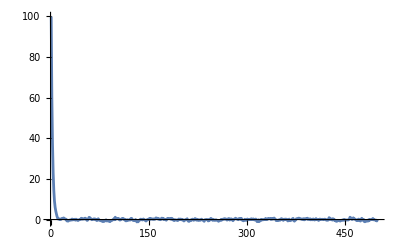

```mathematica
ans1["Path"]//ListLinePlot[#,PlotRange->Full]&
```

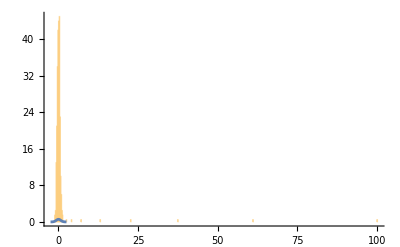

```mathematica
With[{tmp=ans3},

Show[ 
	Histogram[
		WeightedData[tmp["Path"],ConstantArray[1,Dimensions[tmp["Path"]]] / Length[tmp["]Path"]]]
	]
	,
	Plot[( Exp[-k^2]/√π),{k,-2.5,2.5}]
	,
	PlotRange->Full,
	AxesOrigin->Automatic 
]
]
```

#### Action 1

```mathematica
ans1=NPathIntegral[
	actionCompiled[
		action1Compiled,
		harmonicKineticCompiled,
		harmonicPotentialCompiled,
		harmonicVelocityCompiled,
		m,
		k 
	],
	pathEnergyCompiled[ 
		harmonicKineticCompiled,
		harmonicPotentialCompiled,
		harmonicVelocityIndexedCompiled,
		m,
		k
	 ] ,
	(* x *){100,0}
	,
	(* t *){0,250}
	,
	"LatticePoints" -> 500
	,
	"Iterations" -> 1000,
	"ThermilisationLength" -> 1000,
	"NumberOfPaths" -> 3
	,
	"ComputePathEnergy"-> False
	,
	"OptimiseAcceptance"-> True,
	"SelectionThreshold" -> 1,
	"OptimalAcceptanceRate" -> 0.67,
	"OptimalAcceptanceVariant" -> 0.005
]
```

<|E_0 (Numeric)→<|AverageOfAllPaths→31.3643,AverageOfFinalPaths→30.3842|>,E_1 (Numeric)→31.3529,E_0 (Analytical)→0.484375,E_1 (Analytical)→1.45313,E_0 Error [%]→6375.2 %,E_1 Error [%]→2057.62 %,Std. Deviation→5.64808,Path→{100,60.4847,37.4487,23.1157,14.3948,9.09411,6.11098,4.21021,2.74428,1.45914,0.532342,0.190056,0.216733,0.300973,-0.0323132,0.0727593,0.427457,0.632839,0.403245,0.803108,0.574384,0.274764,0.204605,0.11691,-0.696818,-0.548432,-0.788533,-0.432522,-0.244713,-0.280677,-0.349911,-0.0794587,0.252008,-0.210769,0.0575071,-0.0807419,0.152938,-0.322431,0.179073,-0.184793,-0.210779,-0.517402,-0.209932,-0.0778824,0.123583,0.0543124,0.63261,0.36742,0.158631,0.350383,0.301806,0.282442,0.68405,0.462389,-0.0760417,-0.4572,-0.218842,0.526823,1.11031,0.944193,0.484045,0.373091,-0.0862973,0.00294542,0.0293423,0.322967,0.308659,0.309725,-0.126657,-0.0983584,-0.512724,-0.0653242,0.405288,-0.22258,-0.406207,-0.374998,-0.609741,-0.495356,-0.846378,-1.02411,-0.96775,-0.664993,-0.733316,-0.307466,-0.128585,-0.707553,-0.421538,-0.687316,-0.792563,-0.933163,-1.06171,-0.399581,-0.462228,-0.445186,-0.15239,-0.0447093,0.400207,-0.104466,1.13738,0.183423,0.51455,0.51642,0.338778,0.562514,0.037345,-0.255121,-0.168021,0.110705,0.448606,0.313347,0.57574,0.315981,-0.140752,0.0275675,-0.635486,-0.629324,-0.103693,-0.136399,-0.378083,-0.265364,-0.204152,-0.244728,0.543494,0.582502,0.0976963,-0.40406,-0.356024,-0.572923,-0.511572,0.0203282,-0.453268,-1.16168,-0.96654,-1.1327,-0.473062,-0.215917,-0.224774,0.200745,0.0268753,-0.169744,-0.187586,0.264113,-0.0750726,-0.125618,-0.472764,-0.729854,-0.192541,-0.187543,0.117856,0.13195,0.438105,0.0331338,0.591563,0.370154,0.163607,0.189684,0.332237,0.104016,0.098777,0.186356,0.775745,0.745513,0.620961,0.490057,0.119607,0.346302,0.225122,-0.0830362,0.0463422,0.673826,0.632987,0.1923,0.454139,0.0192822,0.0211586,-0.0756355,-0.33063,0.14201,0.589638,0.47567,0.546667,0.501656,0.372768,0.149267,0.617784,0.157148,0.266853,-0.35552,-0.506152,-0.0705837,-0.217691,-0.154208,-0.277837,-0.50624,-0.408795,0.254731,0.176343,0.0148729,0.227013,0.0973206,-0.183461,0.0102934,-0.342316,-0.720431,-0.222873,-0.183706,-0.0116695,-0.00390637,0.403376,-0.532844,-0.86149,-0.89996,-0.326548,-0.201707,-0.523972,-0.10257,0.184338,0.0870264,-0.380067,-0.0525607,0.496822,0.339102,-0.315528,0.110201,-0.29034,-0.438988,-0.0744422,-0.271341,-0.375254,-0.0744664,0.191147,-0.173737,-0.309238,-0.38929,-0.892284,-0.0950388,-0.0252459,-0.00560259,0.0561962,-0.0321997,-0.672595,-0.583462,0.0683507,-0.245269,0.565531,0.43422,-0.0455982,-0.401425,0.0542987,-0.165424,-0.430596,-0.329929,-0.0881293,-0.298685,-0.391899,-0.593378,-0.871858,-0.423381,-0.421652,-0.441826,0.11026,-0.254924,0.123897,0.165351,0.116879,0.423681,0.345272,0.331943,-0.00444811,-0.281443,0.28799,-0.0705695,0.489204,-0.264867,-0.0735009,0.352798,0.234006,-0.233125,-0.571925,-0.158606,0.230254,0.365379,0.672713,0.332383,0.235609,0.100149,-0.105014,0.475264,0.295522,0.469931,0.136599,0.532989,-0.289983,-0.47117,-0.6204,-0.359446,0.144727,-0.266749,-0.448066,-0.119371,0.249147,-0.108775,-0.0415214,0.105029,-0.0681224,0.0866049,0.39902,0.0352504,0.0730841,0.331558,0.00356768,-0.234981,0.164361,0.222022,-0.586749,-1.04789,-0.298764,-0.102659,-1.05147,-0.680498,-0.124783,-0.405545,0.0983903,-0.129182,-0.162529,0.0298716,-0.0295507,-0.00132122,0.551794,-0.0270318,-0.0462188,0.116125,0.581595,0.506448,0.490792,0.502237,0.0507079,0.492453,0.305666,0.130203,0.563594,0.740268,0.357157,0.117187,-0.502269,-0.463982,-0.302696,-0.55742,-0.158689,-0.152277,-0.35148,-0.000968574,0.45295,0.150869,0.165758,-0.420751,0.123757,0.164127,0.0617575,0.252831,-0.129263,-0.0722339,-0.700088,-0.207367,0.21214,-0.535156,-0.551082,-0.295961,-0.192915,0.396914,0.558526,-0.487638,-0.790473,-0.367492,-0.210057,0.374509,0.416827,0.519669,0.627374,0.68572,0.376124,0.441656,0.252876,0.245864,-0.00533631,0.265419,0.424111,-0.158379,0.31654,0.231737,0.455872,0.319571,0.651832,0.00546897,0.107854,0.235349,0.371566,-0.151788,-0.0125143,0.186334,-0.133546,0.273039,-0.075543,-0.23538,0.0241986,0.459651,0.0410895,-0.081871,-0.0268962,-0.446715,-0.0743108,0.259983,0.00562691,0.0224859,0.103984,0.118982,-0.064555,-0.0268693,0.190254,0.140446,-0.000381891,-0.349256,-0.305648,-0.368843,-0.07836,0.921903,0.727383,0.0347961,0.0707365,0.286042,-0.283888,0.391859,0.225888,-0.372928,-0.227313,-0.555879,-0.869826,-0.838823,-0.561316,-0.417717,-0.605918,-0.51461,-0.746766,-0.521421,-0.319526,-0.35579,-0.420357,-0.0129092,-0.00478939,-0.388677,-0.15853,-0.206124,-0.244083,-0.207628,-0.248061,-0.0760665,0.230478,1.13972,0.898831,0.466287,0.0418877,0.138051,0.847899,0.37747,0.352304,0.0527029,-0.0489324,-0.517377,-0.318679,-0.499476,0.225701,0.0604284,-0.568656,-0.745918,0.0224391,0.62127,-0.193959,-0.410757,0.034139,-1.03993,-1.07815,-0.731128,-0.556889,-0.802321,-0.323538,-0.723711,-0.0197464,-0.359832,-0.0828063,0.00663323,0.120379,-0.0628986,0.52526,-0.142496,-0.105809,-0.208748,-0.3461,-0.280263,-0.695444,0},Acceptance→<|n→580523/249000,%→77.7139|>,Timing→<|Thermalisation→21.2233,Main→60.1139,Total→81.3372|>|>

#### Action 2

```mathematica
ans2=NPathIntegral[
	actionCompiled2[
		action2Compiled,
		harmonicKineticCompiled,
		harmonicPotentialCompiled,
		harmonicVelocityCompiled,
		m,
		k 
	],
	pathEnergyCompiled[ 
		harmonicKineticCompiled,
		harmonicPotentialCompiled,
		harmonicVelocityIndexedCompiled,
		m,
		k
	 ],
	(* x *){100,0}
	,
	(* t *){0,250}
	,
	"LatticePoints" -> 500
	,
	"Iterations" -> 1000,
	"ThermilisationLength" -> 1000,
	"NumberOfPaths" -> 3
	,
	"ComputePathEnergy"-> False
	,
	"OptimiseAcceptance"-> True,
	"SelectionThreshold" -> 1,
	"OptimalAcceptanceRate" -> 0.67,
	"OptimalAcceptanceVariant" -> 0.005
]
```

<|E_0 (Numeric)→<|AverageOfAllPaths→20.0908,AverageOfFinalPaths→19.4629|>,E_1 (Numeric)→20.4317,E_0 (Analytical)→0.484375,E_1 (Analytical)→1.45313,E_0 Error [%]→4047.77 %,E_1 Error [%]→1306.05 %,Std. Deviation→4.49788,Path→{100,-0.144877,-0.31931,0.196421,0.605809,0.312335,0.861592,0.682509,0.890354,0.511212,1.19551,0.560377,0.789662,0.772449,0.468406,0.666357,0.583275,0.685001,0.058805,-0.210039,0.0806711,0.483684,0.271991,0.311398,-0.665067,-0.410558,-0.262476,-0.194057,0.271834,1.14266,0.514343,0.527753,0.276477,0.556893,0.751917,-0.131895,-0.721985,0.495117,0.753593,0.0891258,0.459463,-0.016415,0.422934,0.204606,-0.530646,-0.57737,0.245472,0.227574,0.183337,-0.63502,-0.362299,-0.128505,0.0855868,0.0109761,0.252649,0.092212,0.200354,-0.1863,-0.17524,-0.0533206,0.075365,-0.500764,-0.246107,0.683415,0.455139,-0.387636,-0.241116,-0.00880992,-0.543643,-0.838291,-0.539346,-0.583956,-0.977887,-0.680367,-0.718591,-0.395138,-0.419626,-0.0231825,-0.0320092,0.62673,0.713038,1.25533,-0.306822,-0.00793267,-0.0590443,0.451705,0.0101559,0.306894,-0.55524,-0.0042584,-0.316599,-0.656885,-0.536349,-0.0644984,-0.241184,0.514929,0.499877,0.309219,-0.320068,0.668083,0.396209,0.954731,0.291951,0.531644,0.750171,0.278404,0.264196,-0.329325,-0.155064,-0.37595,-0.154537,0.209396,-0.556685,-0.00336741,-0.102333,-0.920926,0.205229,0.541035,0.0773118,0.675127,0.249688,0.090669,-0.500542,0.125033,0.660409,-0.261872,-0.241229,0.216545,0.333043,0.377629,0.0423236,0.853177,-0.118306,-0.469146,0.437693,0.878935,0.371721,0.103975,0.196743,-0.53528,-0.121139,-1.25648,-0.651261,-0.40104,0.425165,0.282377,-0.286511,0.11067,-0.402739,-1.35153,-0.328902,0.17046,0.566924,-0.361947,0.280928,0.19257,-0.248837,0.265036,-0.18801,-0.0490207,0.0553122,0.414594,0.879088,0.651419,0.630929,0.53624,0.658339,0.274669,0.642797,0.112488,-0.579332,-0.50717,0.101257,0.46198,0.158034,0.210497,-0.196442,-0.646906,-0.595594,-0.387675,-0.148375,-0.0888205,0.26819,0.00349387,-0.093096,0.272582,-0.397525,-0.244398,0.176471,0.176739,0.368208,-0.544213,-0.925897,-0.345938,0.439323,0.429505,-0.143302,-0.324875,-0.301747,-0.639326,-1.03924,-0.40854,0.291727,-0.237054,0.198645,-0.440489,0.269582,0.021242,0.232554,-0.146581,-0.0846417,-0.456209,-0.416871,0.0804418,-0.0767998,-0.78802,-0.260981,-0.685991,-0.250571,0.697112,0.579924,-0.416389,-1.04998,-0.799628,-0.741824,-0.390456,0.274822,-0.187027,-0.191739,-0.138007,0.542522,0.868322,0.767033,0.342499,0.0278295,-0.190723,0.398197,0.101812,0.674762,1.06612,0.81547,-0.162549,-0.454364,-0.111117,-0.0307098,0.121875,-0.453512,-0.536646,-0.553303,-0.562267,0.426373,0.823748,1.17554,0.696288,0.754658,0.708094,0.139839,-0.374496,0.295345,-0.181634,-0.12533,-0.259856,-0.561242,-0.240849,0.392828,0.219016,0.339453,-0.609365,-0.709317,-0.0830768,-0.543819,0.0441172,-0.368638,0.43508,0.32103,0.810864,0.250874,-0.311789,0.748103,0.681858,0.5772,0.608217,0.0369385,0.378016,-0.448815,-0.433256,0.120759,0.0517418,0.270143,-0.212708,-0.382896,-1.07614,-0.695572,0.263602,-0.0376006,-0.249819,-0.238248,0.490095,0.852448,0.696895,0.44218,-0.0648415,0.0654035,-0.612965,0.47103,-0.274719,-1.00426,-0.23692,-0.0684961,0.277883,1.00243,0.0308629,0.341345,-0.000816054,0.350959,0.436551,0.400976,0.342946,0.305069,0.626468,0.641148,0.343823,-0.0455689,-0.106557,0.0471546,0.487756,0.18584,-0.161689,0.655779,0.474882,0.277378,0.140885,-0.277828,-0.112768,0.178605,-0.0548897,0.248417,1.12966,-0.0362304,-0.73459,-0.527732,-0.35859,0.134962,0.586819,0.951438,0.59381,0.778,1.39817,0.853998,0.32962,0.600153,0.0903996,-0.0778827,-0.426659,0.214965,0.26722,0.554372,1.29862,0.175564,-0.29826,0.0946076,-0.311626,-0.699778,-0.154932,-0.10052,0.412456,-0.177783,0.153534,0.506329,0.221596,-0.215278,-0.730175,-0.0292254,-0.348316,0.345726,0.236603,0.585972,0.428734,0.345239,0.698205,0.607786,0.589018,0.539593,-0.333234,-0.431325,-0.0480071,0.280297,-0.409323,-0.601711,-0.127884,0.410456,0.483595,-0.109157,0.173888,-0.0651071,0.949356,1.22588,-0.12264,-0.200659,-0.246175,0.491098,0.21799,0.113525,-0.259976,-0.0727101,-0.338613,0.346762,-0.126902,0.073416,-1.07858,-0.60021,-0.20761,-0.140206,0.511319,-0.60682,-0.645917,0.035998,-0.149481,-0.615798,-0.336957,0.571701,0.106977,-0.336674,-0.0472997,-0.502525,-0.842049,0.216675,-0.708553,0.0241172,0.302916,-0.1919,-0.79503,-0.488837,0.282183,0.847694,0.467975,0.346057,0.121897,-0.705554,0.257444,-1.15869,-0.827272,-0.510149,-1.15621,-0.108449,-0.281468,-0.204875,-0.559563,-0.0279911,0.359127,0.351814,0.00634846,-0.154094,-0.184278,-1.06458,-0.77574,-0.304516,0.479753,0.154685,-0.194741,-0.398842,-0.675076,-0.167808,-0.109279,0.0739748,0.524655,-0.0907143,-0.571144,-0.401749,-0.483445,-0.296754,-0.465482,0.199326,0.268167,0.634873,0.0191845,0.271762,-0.193058,0.687187,0.201482,-0.0544272,0.332733,0.33838,0.583472,0.0910565,-0.507113,-0.264516,-1.40154,-0.765437,-0.111322,-0.380226,0.106118,-0.641253,-1.29577,-0.88532,-0.688597,0.0264137,-0.227301,0.22366,0},Acceptance→<|n→1153159/498000,%→77.186|>,Timing→<|Thermalisation→16.345,Main→57.5994,Total→73.9445|>|>

#### Action 3

```mathematica
Throw
```

```mathematica
ans3=NPathIntegral[
	actionCompiled3[
		action3Compiled,
		harmonicKineticCompiled,
		harmonicPotentialCompiled,
		harmonicVelocityCompiled,
		k 
	],
	pathEnergyCompiled[ 
		harmonicKineticCompiled,
		harmonicPotentialCompiled,
		harmonicVelocityIndexedCompiled,
		k
	 ]
	 ,
	(* x *){100,0}
	,
	(* t *){0,250}
	,
	"LatticePoints" -> 500
	,
	"Iterations" -> 1000,
	"ThermilisationLength" -> 10,
	"NumberOfPaths" -> 3
	,
	"ComputePathEnergy"-> False
	,
	"OptimiseAcceptance"-> True,
	"SelectionThreshold" -> 1,
	"OptimalAcceptanceRate" -> 0.67,
	"OptimalAcceptanceVariant" -> 0.005
];
```

```mathematica
Dataset[ans3]
```

```mathematica
{
			{tmp1, tmp2},
			{
				tmp3,
				tmp4,
				tmp5
			}
		}=tmp
```

{{41.7567,{{100,61.7281,36.9263,22.7709,13.5959,8.55173,4.80915,3.20215,1.0504,2.22344,0.842088,0.0654589,-0.375487,-0.345404,-0.237984,-1.18809,-0.0103517,-0.237056,-0.385779,0.919509,-0.0660267,-0.332507,0.216772,-0.550642,-0.658286,-0.0301489,-0.0264899,-0.206596,0.38417,-0.426614,-0.805112,-1.09692,0.398731,0.704279,0.243075,0.772841,0.661005,-0.181921,-0.139612,-0.208003,0.541254,1.01451,1.19728,0.0238658,-0.280637,-0.686013,0.322242,0.123415,0.370606,0.302956,0.174729,-0.171138,-0.645894,-0.145974,-0.144469,-0.326616,0.107506,-0.202899,0.98481,0.319309,-0.0158729,-0.909716,-0.929507,-0.361526,-1.0389,-0.780123,0.85192,0.988515,-0.103763,0.670843,1.20093,1.26259,2.01235,0.988801,0.856947,0.812107,0.858594,0.715975,0.413171,-0.603019,0.057862,0.452085,0.305202,1.03217,1.19438,0.317264,2.49729,1.61788,1.11851,0.587751,0.0494111,0.226799,-0.242436,0.353006,-0.121071,0.00410553,-0.938152,0.10313,0.176054,-0.554104,-0.591901,-0.48565,0.242122,0.386525,0.714367,0.394762,1.01578,0.820783,1.27649,0.358873,0.0166741,-0.591234,-1.53167,-0.887038,0.226195,0.906225,0.0267192,0.365397,0.127956,0.634139,-0.116379,-0.0714956,-0.179931,-0.0552512,0.359726,0.336497,-0.0061839,-0.372691,0.734172,1.0892,1.28963,1.64653,1.28224,-0.250631,-0.0687977,0.138529,0.376757,-0.360311,-0.0500399,0.545501,0.941436,0.968184,0.363672,1.37897,1.79576,1.76704,0.649469,-0.460655,-1.21016,-0.704391,0.119082,-0.0264573,0.772412,1.61873,1.12714,2.15412,1.75026,1.74655,1.09331,-0.169026,-0.214373,0.708176,1.39175,0.378348,0.580489,-0.152064,-1.16475,-1.28801,-1.34029,-0.898755,-0.855885,-0.429615,-0.628053,-0.330203,-0.155927,-1.5003,-1.44564,-0.863034,-1.75827,-2.18116,-0.93949,0.252361,-0.264377,-0.38782,-0.607061,-0.791805,-0.624887,-1.2497,-1.07446,0.148887,0.620073,0.69769,0.267587,-0.258402,-0.602858,-0.0746951,-0.768726,-0.58486,-0.588368,0.137043,0.459718,1.34247,1.1444,0.52922,0.937698,-0.028857,-0.0948594,-0.330674,-0.802936,-0.162576,-0.661737,-0.504948,0.219201,-0.219965,-1.01346,-0.0785298,0.92625,1.06734,1.63651,2.12177,0.935388,0.485996,0.666975,-0.164945,0.251831,0.0790325,-0.436053,-0.453014,-0.0869739,-0.199263,0.607027,0.0820753,0.0388139,1.41729,1.17687,0.717446,0.540868,0.108235,1.23066,-0.192411,0.351762,0.300808,-0.127073,-0.407486,-0.632679,-0.215653,-1.00353,-1.23385,-0.828544,0.205834,-0.10679,-0.370722,0.849562,0.521706,0.919051,0.769192,1.16222,0.869603,0.231494,-0.210922,0.426525,0.506708,1.52257,0.997928,1.10302,0.143927,0.649254,0.27783,0.0398783,-0.364305,-0.806252,-0.446891,-0.551625,-0.934033,0.241866,0.464465,0.808156,0.800509,0.776948,0.143641,0.0683192,-0.0963988,0.171341,0.718561,-0.151901,-0.088103,0.278228,-0.643081,-0.738592,-1.43029,0.198368,0.620836,0.584431,0.521397,0.844997,0.507904,0.754478,1.10082,0.831941,0.0882903,-0.328513,-0.478619,0.366678,-0.632294,-0.954162,-0.121657,-0.285327,-0.292496,-0.0445669,-0.256537,0.513454,0.578153,0.989817,-0.289062,-0.634031,0.459937,0.904324,0.232088,0.748505,-0.248382,-0.474557,-0.616661,0.119448,0.385509,-0.180517,0.280243,0.945614,1.82085,0.117756,-0.126293,-0.455654,-0.574177,0.323611,0.725933,0.952932,2.00887,0.63538,0.49066,0.125677,0.160757,-0.507763,-0.286835,-0.208162,0.0701063,0.00277883,0.366871,0.208377,0.62646,1.1468,0.00640523,0.0909726,0.354539,1.15536,0.571842,0.505743,0.226086,-0.110424,0.65103,0.534931,-0.784215,0.54181,0.214621,-0.269083,-0.268548,0.427645,-0.296505,0.696312,1.57395,1.53586,0.463239,1.09759,1.43967,1.10061,0.101838,0.353979,0.708882,0.470154,1.16071,0.145129,-0.479598,-0.619319,0.789717,0.748524,-0.32082,-0.714634,0.538379,-0.0589212,-0.0496434,-0.0458682,-0.0998861,0.144582,0.599592,1.01448,1.13031,0.383649,0.0673656,0.192408,0.754249,-0.117755,-0.692462,-0.24541,-0.880293,-0.54567,-1.411,-0.556918,-0.387027,0.175764,-0.247479,0.469503,0.584195,0.0273735,-0.0327196,-0.396697,-0.133011,-0.801238,-0.481729,-0.73976,-1.10362,-1.91944,-2.50431,-2.59095,-1.40097,-0.857552,-0.326755,-0.468932,0.171759,-0.379538,0.0542907,0.564964,-0.0390134,0.463416,1.56552,0.758868,0.773007,-0.139371,-0.219283,0.589601,0.545059,0.554606,1.1571,0.697713,0.0121726,1.07588,0.82729,0.769007,0.664206,-0.245526,-0.230908,0.103903,-0.305419,0.21354,0.311718,0.33065,1.41418,1.15604,0.0243586,-0.311999,0.207355,0.544524,0.736328,0.569108,1.18146,0.250397,1.02363,1.17475,0.73927,1.62397,0.671787,0.601808,0.343743,-1.17936,-0.868553,-0.271114,-0.0972312,-0.160136,-1.26347,-0.89029,-0.342745,-0.559209,-1.06888,-0.700938,-0.00773919,-1.25838,-2.45486,-2.27885,-1.57059,-1.01838,-0.831332,-0.848335,-0.919541,0.593111,0.729901,-0.400893,-0.660262,-0.552122,-0.630666,-0.268711,-0.287762,0.0745527,0},{100,60.0703,36.589,21.6038,13.223,9.06902,5.49872,3.95926,2.20298,1.2036,0.246943,-0.31911,-0.036012,-0.387072,-0.742577,-0.632755,-0.896135,0.183379,0.258568,-0.888496,-0.250883,-1.20632,-0.153172,1.06459,0.757668,0.0684379,0.67249,-0.0187894,0.279684,0.777365,-0.842283,-1.01284,-0.569323,-0.14068,0.0966532,0.0671639,0.25099,0.0550461,0.0713654,0.71102,0.165137,-0.83544,-0.089204,0.143908,-0.0799155,-0.109608,-0.809502,-1.20315,0.349356,-0.0103337,0.423154,-0.300118,-0.0753509,0.127753,-0.413159,-0.556268,-0.303837,-0.141477,-0.741246,-0.267551,-0.184176,0.58343,-0.158564,0.835706,-0.0937904,0.233787,0.448221,-0.065328,-0.0496492,-0.531477,-0.567173,0.0805232,0.346499,-0.004088,-0.590214,0.306118,0.0463249,-0.548363,-0.137894,-0.717756,-0.368085,-0.470471,-0.0526195,0.357562,0.0166824,-1.2015,-0.541196,0.17045,0.180945,0.0507882,0.305355,0.303847,0.248245,-0.106719,0.30764,0.674495,0.30712,-0.426441,-0.418257,-0.025145,-0.661448,0.223218,-0.563228,0.241154,0.200383,0.384244,0.0654358,0.981586,0.316641,-0.733007,-0.603561,-0.898784,-1.50281,-0.105203,-0.640366,-1.23343,-0.259597,0.708107,0.528055,0.57132,-0.397437,-0.145793,-0.230494,-1.00031,-0.62179,-0.457085,-0.204904,-0.0141775,0.245226,0.127402,-0.727187,0.239858,0.777018,0.368631,-0.335172,0.604782,0.178098,0.284762,0.283028,0.481495,0.323602,0.876067,0.9054,0.457171,0.252794,0.791182,0.414209,0.799434,-0.417836,-0.474186,0.081343,0.0354629,0.393632,1.2729,1.13212,1.18045,1.69157,0.508694,-0.812138,-0.6696,-0.228307,-0.87285,-0.486011,-0.228538,-0.672723,-0.258124,-0.892196,-0.522496,-0.237765,-0.500329,-0.932428,-0.876108,-0.526591,-0.140006,0.0780262,0.45542,-0.343088,0.192705,0.667034,-0.168291,0.558977,0.306196,0.668176,-0.157493,-0.439046,0.395669,0.496391,0.727602,-0.415233,-1.21819,-1.02249,-0.589457,-0.604281,-0.0777964,-0.650547,0.141884,0.224288,-0.173723,0.647852,0.172473,-0.33839,-0.500242,0.23699,-0.326288,-0.198611,-0.239657,0.724645,1.47272,0.871333,-0.150422,-0.0259379,1.10887,0.475485,0.443357,0.552462,0.0202001,-0.0663166,0.931313,0.309644,1.15196,0.0578466,-0.165734,-1.05544,-0.636597,-0.541568,-0.539393,-0.0364589,-0.725477,-0.968236,-0.756349,-0.380242,-0.377678,0.778074,0.191948,0.360948,-0.0404367,-0.387733,-0.533554,-0.81832,-0.570636,0.106349,0.0931753,0.050122,-0.252377,-0.193523,-0.040727,0.828127,1.2695,1.36044,1.59028,0.470563,0.284824,0.219692,0.34908,-0.230065,1.02521,-0.267667,-0.303772,0.656392,-0.487,-0.495151,-0.694358,0.00480718,-0.363706,0.395695,-0.285801,-0.376022,-0.288603,-0.00568403,-0.559334,-0.181817,-0.166955,0.353881,-0.398016,-0.515719,0.19678,0.961035,1.68025,0.95634,0.928265,-0.443101,-0.745495,-0.912444,0.550098,1.22462,0.060121,0.34015,-0.518158,-1.65283,-1.5409,-0.582628,-0.81175,0.061089,-0.03021,-0.208341,-1.54222,-0.300246,-0.267025,0.472156,0.770127,-0.489659,-0.679599,-0.850599,-0.00313282,0.382325,0.490946,-0.0101938,-0.0641907,0.469811,0.180595,0.364709,-0.087763,-0.0193445,-0.0836848,-0.258907,0.695043,0.857329,0.386908,0.980263,1.21144,-0.276036,-0.572504,-0.653207,-0.366386,-0.0673939,0.244902,-0.258802,0.113473,-0.128671,-0.642492,0.313579,-0.358825,-0.50241,0.884617,0.835105,0.191314,-0.0324412,-0.0647295,-1.02137,-0.653816,-0.550045,0.629764,0.407594,0.442763,1.7838,0.579898,-0.207506,0.22802,1.18018,0.0845741,0.192626,0.855035,1.18143,0.40147,0.160592,-0.275216,-0.43856,-0.170998,-0.483895,0.360161,0.425687,1.14815,-0.0568012,-0.229422,0.556049,0.639937,0.61859,0.0295148,0.897324,1.39865,1.18416,0.84602,-0.18238,-0.645587,-0.182956,-0.674602,-0.641241,-0.117307,0.928438,-1.24808,0.228093,-0.684997,-0.617632,-1.11209,-0.889208,-1.27202,0.190213,0.622037,0.849115,0.5588,0.546353,0.918443,1.62322,1.16626,0.491644,-0.242535,-0.681961,-0.425592,0.0322387,-0.341502,0.0269219,0.170903,-0.236736,-0.038742,-0.0493133,-0.401258,-0.136929,-0.0810121,0.303138,0.622732,0.242811,1.33933,0.730581,-0.0654036,0.132813,0.863109,0.979775,-0.252528,-0.836357,-0.728634,-0.552764,-0.651794,-1.30576,-0.937379,-0.819059,-0.462037,-0.159998,0.0118637,1.34812,0.778378,0.39242,1.58604,1.04858,-0.320118,-0.0966279,-0.61251,-0.566462,-0.295056,0.720592,0.405181,0.0920266,0.850788,0.892091,0.733636,0.372869,0.354557,0.452901,0.238953,0.345757,-0.463976,-0.639747,-0.0100256,-0.47094,-1.98,-0.908554,-0.299461,0.0527184,0.293454,-0.540153,-0.111876,1.369,0.441384,-0.418921,-0.824177,-1.337,-0.0804383,0.724617,0.152871,-0.358383,0.0394345,-0.300666,-0.429052,-0.106122,0.329832,0.0400604,0.744934,0.104672,0.763106,0.344509,-0.00667417,0.0702358,-0.913815,0.624967,0.408801,-0.457612,-1.36343,-1.45095,-1.15111,-1.20747,-0.701266,0.0386075,-1.08492,-0.648618,0.24512,0.139329,1.07211,-0.0144008,-0.66643,-0.750491,0},{100,60.994,37.3418,22.1079,14.0035,8.33186,5.72237,4.12921,1.38956,0.821318,0.51095,0.070213,-0.192175,-0.854286,-1.16927,-0.216455,0.0679053,-0.456031,-0.0652527,-0.235285,-0.850254,0.297823,0.724469,0.729016,0.964216,-0.586517,-0.843227,-1.30025,-0.846259,-1.76179,-0.79015,-0.378093,-0.466391,0.182345,-0.89235,-1.02022,-1.43078,-0.528478,-0.470522,0.664153,0.720203,1.59259,0.788351,0.401003,-0.121308,-0.327576,-0.322411,0.592352,0.200997,1.18093,0.837932,0.271413,1.21895,-0.30109,0.0430456,-0.711349,0.244703,-0.222942,-0.0674389,0.0645384,0.619855,0.348339,-0.379131,-0.79837,-0.376546,0.151141,-0.497401,-1.07205,-1.46315,-1.18533,-0.460982,0.0836917,0.672788,0.556615,-0.353539,-0.163588,0.618841,0.108987,0.0856239,-0.015786,0.399131,0.115516,0.654884,1.05502,0.835464,0.00235854,0.106069,-0.481351,-1.54184,-0.989437,-0.263497,0.853843,1.33667,1.05147,0.842339,0.730699,0.540317,-0.219537,0.129789,1.05896,0.140895,0.166735,1.15588,1.23186,0.536248,0.801666,0.819063,0.465034,0.534806,-0.530046,0.45122,-0.0424522,0.243608,-0.0189208,-0.045769,0.538872,0.763896,-0.879195,-0.746872,-0.598645,0.2429,0.181484,0.029242,-0.351085,0.130331,0.272625,-0.336793,-0.499219,-0.173359,-1.56496,-1.09106,-0.366838,-0.854324,-1.31945,-0.0143486,0.102259,0.20389,0.673872,0.593862,0.394052,-0.561951,-0.622583,-1.25439,-1.86234,-1.55563,-0.581675,0.0930224,-0.293594,0.142998,0.636886,0.164084,-0.58181,0.126771,0.386904,-0.444314,0.755415,-0.342409,-0.551417,-0.285975,0.490845,0.190984,-0.365487,-0.725321,-0.63985,-1.60479,-0.646881,0.159393,0.71402,0.585777,0.780092,1.47087,0.492092,0.361226,0.017545,-0.340288,0.622768,0.230031,-0.798376,-0.278315,-0.0440231,0.712996,-0.312392,-0.600855,-0.300237,-0.567189,0.14667,-0.807016,-0.315772,0.277019,-0.0343757,0.236357,0.523366,0.631796,0.795422,0.808083,0.202316,0.560954,0.581367,-0.0815445,0.302867,0.218458,-0.189124,0.586812,-0.348069,0.129624,0.319025,0.816425,0.72181,0.465504,-0.0902232,-0.168784,0.0953095,-0.645685,-0.370767,-0.0618043,-0.453138,-1.13016,-0.878868,-0.614307,0.0179665,-0.254885,1.31186,0.0717427,0.0799166,-0.188152,0.359207,-0.148707,-0.812628,0.500874,0.695774,0.160152,-0.835846,-0.719063,0.674538,0.539105,-0.304343,-0.214923,0.108022,-0.322186,0.461096,0.637158,-0.53404,0.00912795,0.363415,0.559485,-0.234483,-0.61665,0.2875,0.451902,0.489149,-0.523013,-1.04421,0.0679986,0.609698,0.634492,-0.512954,-0.43588,0.459293,1.04043,1.24818,1.52988,1.17032,0.228549,-0.294441,-1.19376,-0.418744,0.505803,0.173092,-0.110863,-0.133136,-0.598447,0.0990871,0.168946,-0.0869857,0.67964,0.412212,-0.0275798,0.353317,-0.160355,0.805853,1.26388,0.706794,-0.615803,0.295491,0.667253,0.869184,0.663395,0.13463,-0.0694023,-0.11664,0.409085,0.113046,0.842736,1.02969,-0.845425,-0.95563,-0.8592,-0.673058,-0.822178,-0.93413,-0.519037,-1.22434,-0.728469,-1.27117,-0.5585,-0.180498,-0.491545,-0.372384,0.424286,0.659951,1.03529,-0.288918,-0.102328,0.464245,1.14371,0.796562,0.721906,0.822388,0.362891,0.29859,0.292553,0.486372,-0.101229,-0.27859,-0.259116,-0.720994,0.0554408,0.739752,-0.0871033,0.202647,0.647687,0.745915,0.443342,0.567196,0.255,0.54261,0.555581,0.172219,-0.670957,-0.0876316,-1.44032,-0.880546,1.50291,0.433697,0.858463,-0.321007,0.315087,0.333088,0.414064,-0.344769,-0.545916,-0.649334,-0.00479215,0.0705743,-0.0343715,-0.215183,-0.68441,-0.773468,-0.589411,-0.0303697,0.234696,0.578334,0.347019,1.40357,1.18239,0.984876,0.933713,0.528617,-0.0940901,-1.69588,-1.37515,-0.60047,-0.503674,-0.580408,-0.260885,0.249721,0.687177,0.69828,0.488268,0.410419,0.177838,-0.326363,-0.788035,-0.0785714,0.521253,0.524082,1.74651,0.813854,0.619984,-0.68863,-1.78476,-1.08019,-1.16004,0.558957,0.515106,0.48462,-0.409575,-0.500788,0.402391,0.927056,0.510675,0.542823,1.04999,0.383895,-0.230462,0.521328,0.409978,-0.348244,-0.663711,-0.260983,-0.795541,-0.646237,-0.95056,-1.14384,-1.22964,-0.572953,-1.0238,-1.25509,-1.5203,-0.79182,-1.68521,-2.41133,-1.51999,-0.35162,-0.992053,0.0561717,-0.618575,-0.282701,1.10425,0.67733,0.245784,0.492434,0.466925,-0.0766055,0.394097,-1.18943,-0.946463,-0.0685866,-0.125769,-0.436329,0.217201,-0.152526,-0.175307,-0.286281,-0.974324,-0.527763,-0.240922,0.132162,-0.306812,-0.630852,-0.575937,-0.158929,-0.625672,-0.010004,0.0864807,-0.0404232,-0.722178,-0.0228913,-1.37208,-0.406242,-0.519317,-0.035828,-0.307967,0.973669,0.748283,1.40849,0.871598,1.41371,0.582719,0.687048,-0.446368,-0.491907,-0.0325176,0.394254,-0.476985,-0.102434,0.869807,0.46933,1.53364,0.667965,-0.286291,0.74479,0.924086,0.191392,-0.546903,0.370457,-0.282466,-0.17601,0.618777,0.0605458,0.402229,0.423405,0.273514,-0.779922,-0.289746,-0.45487,-0.532851,0.440047,1.29756,0}}},{{{{298,149/249},{300,50/83},{313,313/498},{335,335/498},{323,323/498},{313,313/498},{313,313/498},{299,299/498},{310,155/249},{302,151/249},{298,149/249},{296,148/249},{315,105/166},{336,56/83},{307,307/498},{315,105/166},{325,325/498},{299,299/498},{298,149/249},{301,301/498},{326,163/249},{324,54/83},{310,155/249},{341,341/498},{305,305/498},{306,51/83},{316,158/249},{311,311/498},{306,51/83},{305,305/498},{294,49/83},{301,301/498},{318,53/83},{303,101/166},{307,307/498},{296,148/249},{299,299/498},{327,109/166},{305,305/498},{290,145/249},{285,95/166},{310,155/249},{303,101/166},{279,93/166},{299,299/498},{298,149/249},{317,317/498},{308,154/249},{332,2/3},{311,311/498},{289,289/498},{289,289/498},{301,301/498},{302,151/249},{328,164/249},{319,319/498},{305,305/498},{310,155/249},{297,99/166},{300,50/83},{312,52/83},{331,331/498},{320,160/249},{310,155/249},{290,145/249},{318,53/83},{311,311/498},{314,157/249},{304,152/249},{325,325/498},{302,151/249},{311,311/498},{296,148/249},{289,289/498},{286,143/249},{297,99/166},{303,101/166},{303,101/166},{318,53/83},{302,151/249},{328,164/249},{304,152/249},{308,154/249},{307,307/498},{313,313/498},{290,145/249},{316,158/249},{315,105/166},{300,50/83},{290,145/249},{303,101/166},{329,329/498},{310,155/249},{309,103/166},{302,151/249},{318,53/83},{299,299/498},{332,2/3},{310,155/249},{296,148/249},{302,151/249},{298,149/249},{312,52/83},{304,152/249},{310,155/249},{327,109/166},{324,54/83},{308,154/249},{295,295/498},{298,149/249},{310,155/249},{310,155/249},{328,164/249},{309,103/166},{298,149/249},{305,305/498},{312,52/83},{332,2/3},{319,319/498},{280,140/249},{287,287/498},{315,105/166},{300,50/83},{294,49/83},{293,293/498},{312,52/83},{304,152/249},{288,48/83},{307,307/498},{307,307/498},{307,307/498},{331,331/498},{303,101/166},{318,53/83},{303,101/166},{290,145/249},{310,155/249},{302,151/249},{309,103/166},{313,313/498},{326,163/249},{306,51/83},{292,146/249},{323,323/498},{291,97/166},{307,307/498},{317,317/498},{299,299/498},{302,151/249},{319,319/498},{311,311/498},{309,103/166},{308,154/249},{320,160/249},{314,157/249},{319,319/498},{311,311/498},{311,311/498},{317,317/498},{303,101/166},{309,103/166},{311,311/498},{315,105/166},{297,99/166},{311,311/498},{289,289/498},{322,161/249},{310,155/249},{290,145/249},{311,311/498},{302,151/249},{322,161/249},{313,313/498},{312,52/83},{303,101/166},{307,307/498},{325,325/498},{311,311/498},{314,157/249},{316,158/249},{300,50/83},{313,313/498},{307,307/498},{318,53/83},{323,323/498},{325,325/498},{309,103/166},{304,152/249},{329,329/498},{331,331/498},{319,319/498},{307,307/498},{310,155/249},{314,157/249},{319,319/498},{306,51/83},{300,50/83},{295,295/498},{308,154/249},{312,52/83},{305,305/498},{313,313/498},{324,54/83},{309,103/166},{313,313/498},{317,317/498},{322,161/249},{319,319/498},{299,299/498},{297,99/166},{303,101/166},{302,151/249},{296,148/249},{332,2/3},{327,109/166},{301,301/498},{332,2/3},{318,53/83},{306,51/83},{303,101/166},{303,101/166},{297,99/166},{331,331/498},{294,49/83},{294,49/83},{308,154/249},{301,301/498},{301,301/498},{315,105/166},{311,311/498},{326,163/249},{322,161/249},{291,97/166},{292,146/249},{310,155/249},{295,295/498},{284,142/249},{300,50/83},{299,299/498},{307,307/498},{295,295/498},{318,53/83},{308,154/249},{292,146/249},{292,146/249},{309,103/166},{309,103/166},{307,307/498},{307,307/498},{327,109/166},{321,107/166},{311,311/498},{306,51/83},{322,161/249},{305,305/498},{309,103/166},{310,155/249},{292,146/249},{310,155/249},{310,155/249},{301,301/498},{316,158/249},{322,161/249},{309,103/166},{321,107/166},{309,103/166},{313,313/498},{299,299/498},{292,146/249},{292,146/249},{298,149/249},{304,152/249},{287,287/498},{313,313/498},{316,158/249},{295,295/498},{313,313/498},{295,295/498},{319,319/498},{316,158/249},{297,99/166},{314,157/249},{291,97/166},{292,146/249},{300,50/83},{310,155/249},{315,105/166},{312,52/83},{326,163/249},{304,152/249},{295,295/498},{296,148/249},{318,53/83},{316,158/249},{308,154/249},{305,305/498},{284,142/249},{319,319/498},{312,52/83},{306,51/83},{315,105/166},{312,52/83},{316,158/249},{294,49/83},{310,155/249},{303,101/166},{298,149/249},{310,155/249},{306,51/83},{310,155/249},{309,103/166},{302,151/249},{311,311/498},{319,319/498},{316,158/249},{319,319/498},{304,152/249},{301,301/498},{298,149/249},{328,164/249},{307,307/498},{319,319/498},{313,313/498},{307,307/498},{324,54/83},{301,301/498},{309,103/166},{311,311/498},{294,49/83},{316,158/249},{335,335/498},{300,50/83},{327,109/166},{303,101/166},{313,313/498},{299,299/498},{309,103/166},{312,52/83},{312,52/83},{316,158/249},{301,301/498},{307,307/498},{303,101/166},{304,152/249},{316,158/249},{295,295/498},{314,157/249},{301,301/498},{302,151/249},{307,307/498},{305,305/498},{325,325/498},{313,313/498},{315,105/166},{290,145/249},{305,305/498},{317,317/498},{300,50/83},{314,157/249},{294,49/83},{317,317/498},{295,295/498},{305,305/498},{305,305/498},{320,160/249},{321,107/166},{311,311/498},{306,51/83},{312,52/83},{311,311/498},{310,155/249},{297,99/166},{305,305/498},{315,105/166},{298,149/249},{315,105/166},{297,99/166},{315,105/166},{304,152/249},{311,311/498},{328,164/249},{308,154/249},{306,51/83},{326,163/249},{306,51/83},{303,101/166},{309,103/166},{318,53/83},{305,305/498},{310,155/249},{291,97/166},{314,157/249},{307,307/498},{327,109/166},{307,307/498},{320,160/249},{309,103/166},{306,51/83},{314,157/249},{305,305/498},{297,99/166},{312,52/83},{294,49/83},{320,160/249},{292,146/249},{294,49/83},{278,139/249},{283,283/498},{328,164/249},{311,311/498},{307,307/498},{322,161/249},{309,103/166},{311,311/498},{321,107/166},{303,101/166},{308,154/249},{304,152/249},{317,317/498},{300,50/83},{307,307/498},{301,301/498},{306,51/83},{302,151/249},{305,305/498},{316,158/249},{296,148/249},{300,50/83},{308,154/249},{306,51/83},{306,51/83},{303,101/166},{287,287/498},{306,51/83},{325,325/498},{304,152/249},{310,155/249},{290,145/249},{312,52/83},{314,157/249},{288,48/83},{325,325/498},{336,56/83},{306,51/83},{313,313/498},{325,325/498},{312,52/83},{314,157/249},{278,139/249},{322,161/249},{303,101/166},{296,148/249},{322,161/249},{299,299/498},{302,151/249},{310,155/249},{323,323/498},{323,323/498},{320,160/249},{303,101/166},{300,50/83},{304,152/249},{302,151/249},{305,305/498},{319,319/498},{291,97/166},{298,149/249},{313,313/498},{317,317/498},{329,329/498},{317,317/498},{300,50/83},{326,163/249},{308,154/249},{301,301/498},{310,155/249},{304,152/249},{302,151/249},{301,301/498},{322,161/249},{330,55/83},{291,97/166},{296,148/249},{313,313/498},{307,307/498},{289,289/498},{318,53/83},{305,305/498},{305,305/498},{317,317/498},{331,331/498},{333,111/166},{323,323/498},{314,157/249},{321,107/166},{319,319/498},{310,155/249},{325,325/498},{289,289/498},{307,307/498},{297,99/166},{310,155/249},{321,107/166},{314,157/249},{306,51/83},{317,317/498},{297,99/166},{316,158/249},{314,157/249},{317,317/498},{314,157/249},{305,305/498},{282,47/83},{307,307/498},{313,313/498},{302,151/249},{313,313/498},{309,103/166},{298,149/249},{286,143/249},{310,155/249},{313,313/498},{299,299/498},{317,317/498},{321,107/166},{309,103/166},{316,158/249},{317,317/498},{318,53/83},{299,299/498},{317,317/498},{300,50/83},{302,151/249},{312,52/83},{317,317/498},{312,52/83},{306,51/83},{319,319/498},{306,51/83},{291,97/166},{291,97/166},{321,107/166},{308,154/249},{314,157/249},{321,107/166},{309,103/166},{292,146/249},{287,287/498},{305,305/498},{292,146/249},{305,305/498},{294,49/83},{281,281/498},{307,307/498},{321,107/166},{307,307/498},{304,152/249},{297,99/166},{294,49/83},{318,53/83},{315,105/166},{301,301/498},{308,154/249},{303,101/166},{312,52/83},{318,53/83},{315,105/166},{288,48/83},{320,160/249},{331,331/498},{306,51/83},{291,97/166},{316,158/249},{307,307/498},{322,161/249},{328,164/249},{316,158/249},{302,151/249},{294,49/83},{318,53/83},{315,105/166},{309,103/166},{308,154/249},{313,313/498},{319,319/498},{318,53/83},{311,311/498},{290,145/249},{306,51/83},{316,158/249},{319,319/498},{294,49/83},{302,151/249},{292,146/249},{305,305/498},{297,99/166},{295,295/498},{312,52/83},{301,301/498},{294,49/83},{311,311/498},{300,50/83},{295,295/498},{298,149/249},{315,105/166},{300,50/83},{321,107/166},{289,289/498},{309,103/166},{314,157/249},{313,313/498},{326,163/249},{309,103/166},{275,275/498},{316,158/249},{305,305/498},{300,50/83},{317,317/498},{295,295/498},{310,155/249},{278,139/249},{319,319/498},{309,103/166},{314,157/249},{316,158/249},{302,151/249},{303,101/166},{294,49/83},{303,101/166},{325,325/498},{297,99/166},{299,299/498},{313,313/498},{323,323/498},{315,105/166},{306,51/83},{309,103/166},{310,155/249},{305,305/498},{320,160/249},{294,49/83},{302,151/249},{298,149/249},{304,152/249},{315,105/166},{306,51/83},{310,155/249},{307,307/498},{328,164/249},{308,154/249},{322,161/249},{319,319/498},{295,295/498},{303,101/166},{298,149/249},{294,49/83},{309,103/166},{292,146/249},{314,157/249},{293,293/498},{287,287/498},{293,293/498},{289,289/498},{305,305/498},{308,154/249},{318,53/83},{310,155/249},{308,154/249},{318,53/83},{282,47/83},{310,155/249},{316,158/249},{316,158/249},{312,52/83},{296,148/249},{299,299/498},{301,301/498},{314,157/249},{295,295/498},{309,103/166},{314,157/249},{283,283/498},{319,319/498},{316,158/249},{301,301/498},{332,2/3},{319,319/498},{324,54/83},{301,301/498},{310,155/249},{314,157/249},{327,109/166},{313,313/498},{304,152/249},{305,305/498},{304,152/249},{321,107/166},{311,311/498},{325,325/498},{310,155/249},{307,307/498},{309,103/166},{304,152/249},{309,103/166},{310,155/249},{311,311/498},{323,323/498},{320,160/249},{317,317/498},{312,52/83},{307,307/498},{295,295/498},{309,103/166},{312,52/83},{302,151/249},{290,145/249},{311,311/498},{316,158/249},{319,319/498},{304,152/249},{306,51/83},{294,49/83},{314,157/249},{313,313/498},{308,154/249},{300,50/83},{307,307/498},{293,293/498},{321,107/166},{317,317/498},{329,329/498},{319,319/498},{317,317/498},{306,51/83},{316,158/249},{304,152/249},{307,307/498},{304,152/249},{315,105/166},{283,283/498},{297,99/166},{279,93/166},{299,299/498},{320,160/249},{301,301/498},{298,149/249},{309,103/166},{330,55/83},{318,53/83},{308,154/249},{327,109/166},{306,51/83},{313,313/498},{304,152/249},{317,317/498},{306,51/83},{318,53/83},{285,95/166},{305,305/498},{314,157/249},{307,307/498},{290,145/249},{297,99/166},{316,158/249},{297,99/166},{313,313/498},{326,163/249},{321,107/166},{311,311/498},{301,301/498},{305,305/498},{306,51/83},{323,323/498},{313,313/498},{305,305/498},{319,319/498},{319,319/498},{324,54/83},{309,103/166},{314,157/249},{294,49/83},{303,101/166},{321,107/166},{299,299/498},{312,52/83},{316,158/249},{303,101/166},{321,107/166},{324,54/83},{307,307/498},{312,52/83},{299,299/498},{292,146/249},{292,146/249},{292,146/249},{298,149/249},{304,152/249},{298,149/249},{313,313/498},{320,160/249},{284,142/249},{312,52/83},{319,319/498},{313,313/498},{278,139/249},{312,52/83},{320,160/249},{307,307/498},{315,105/166},{313,313/498},{287,287/498},{303,101/166},{309,103/166},{297,99/166},{323,323/498},{307,307/498},{300,50/83},{313,313/498},{300,50/83},{294,49/83},{319,319/498},{305,305/498},{318,53/83},{297,99/166},{310,155/249},{303,101/166},{300,50/83},{307,307/498},{320,160/249},{293,293/498},{311,311/498},{303,101/166},{314,157/249},{320,160/249},{306,51/83},{309,103/166},{303,101/166},{301,301/498},{315,105/166},{314,157/249},{322,161/249},{309,103/166},{319,319/498},{291,97/166},{318,53/83},{294,49/83},{306,51/83},{305,305/498},{282,47/83},{318,53/83},{307,307/498},{316,158/249},{321,107/166},{291,97/166},{325,325/498},{310,155/249},{309,103/166},{300,50/83},{310,155/249},{300,50/83},{312,52/83},{304,152/249},{326,163/249},{300,50/83},{322,161/249},{318,53/83},{313,313/498},{302,151/249},{332,2/3},{309,103/166},{306,51/83},{347,347/498},{311,311/498},{309,103/166},{315,105/166},{309,103/166},{298,149/249},{305,305/498},{301,301/498},{325,325/498},{310,155/249},{320,160/249},{311,311/498},{311,311/498},{312,52/83},{316,158/249},{298,149/249},{317,317/498},{314,157/249},{314,157/249},{283,283/498},{303,101/166},{317,317/498},{313,313/498},{294,49/83},{305,305/498},{308,154/249},{309,103/166},{305,305/498},{321,107/166},{328,164/249},{293,293/498},{306,51/83},{320,160/249},{328,164/249},{337,337/498},{308,154/249},{319,319/498},{323,323/498},{307,307/498},{315,105/166},{308,154/249},{312,52/83},{312,52/83},{303,101/166},{307,307/498},{303,101/166},{297,99/166},{305,305/498},{299,299/498},{293,293/498},{288,48/83},{312,52/83},{302,151/249},{325,325/498},{317,317/498},{328,164/249},{309,103/166},{304,152/249},{296,148/249},{318,53/83},{326,163/249},{309,103/166},{315,105/166},{300,50/83},{315,105/166},{298,149/249},{314,157/249},{309,103/166},{307,307/498},{310,155/249},{316,158/249},{314,157/249},{335,335/498},{286,143/249},{323,323/498},{311,311/498},{309,103/166},{318,53/83},{318,53/83},{314,157/249},{312,52/83},{316,158/249},{317,317/498},{304,152/249},{285,95/166},{298,149/249},{323,323/498},{294,49/83},{288,48/83},{307,307/498},{319,319/498},{316,158/249},{304,152/249},{299,299/498},{293,293/498},{300,50/83},{316,158/249},{313,313/498},{300,50/83},{301,301/498},{316,158/249},{301,301/498},{313,313/498},{305,305/498},{321,107/166},{314,157/249},{315,105/166},{320,160/249},{331,331/498},{297,99/166},{316,158/249},{318,53/83},{286,143/249},{314,157/249},{321,107/166},{306,51/83},{309,103/166},{293,293/498},{300,50/83},{323,323/498},{317,317/498},{299,299/498},{325,325/498},{288,48/83},{301,301/498},{300,50/83},{308,154/249},{316,158/249},{296,148/249},{324,54/83},{316,158/249},{293,293/498},{315,105/166},{322,161/249},{281,281/498},{303,101/166},{318,53/83},{318,53/83},{313,313/498},{309,103/166},{293,293/498},{301,301/498},{306,51/83},{299,299/498},{324,54/83},{320,160/249},{305,305/498},{328,164/249},{296,148/249},{297,99/166},{298,149/249},{314,157/249},{319,319/498},{305,305/498},{313,313/498},{306,51/83},{304,152/249},{295,295/498},{307,307/498},{333,111/166},{303,101/166},{301,301/498},{315,105/166},{307,307/498},{304,152/249},{321,107/166},{321,107/166},{317,317/498},{321,107/166},{291,97/166},{305,305/498},{296,148/249},{313,313/498},{297,99/166},{298,149/249},{311,311/498},{309,103/166},{321,107/166},{301,301/498},{303,101/166},{300,50/83},{320,160/249},{321,107/166},{312,52/83},{316,158/249},{305,305/498},{328,164/249},{309,103/166},{337,337/498},{318,53/83},{330,55/83},{294,49/83},{312,52/83},{303,101/166},{327,109/166},{320,160/249},{326,163/249},{303,101/166},{303,101/166},{306,51/83},{326,163/249},{299,299/498},{298,149/249},{313,313/498},{317,317/498},{297,99/166},{322,161/249},{324,54/83},{303,101/166},{295,295/498},{307,307/498},{310,155/249},{309,103/166},{309,103/166},{323,323/498},{294,49/83},{298,149/249},{319,319/498},{325,325/498},{301,301/498},{309,103/166},{310,155/249},{310,155/249},{304,152/249},{286,143/249},{318,53/83},{300,50/83},{313,313/498},{299,299/498},{304,152/249},{297,99/166},{302,151/249},{326,163/249},{307,307/498},{289,289/498},{322,161/249},{311,311/498},{311,311/498},{323,323/498},{319,319/498},{314,157/249},{308,154/249},{307,307/498},{304,152/249},{316,158/249},{303,101/166},{322,161/249},{310,155/249},{297,99/166},{286,143/249},{287,287/498},{328,164/249},{306,51/83},{313,313/498},{309,103/166},{305,305/498},{306,51/83},{295,295/498},{313,313/498},{287,287/498},{296,148/249},{303,101/166},{331,331/498},{319,319/498},{301,301/498},{313,313/498},{327,109/166},{323,323/498},{311,311/498},{307,307/498},{297,99/166},{309,103/166},{315,105/166},{329,329/498},{295,295/498},{302,151/249},{297,99/166},{298,149/249},{296,148/249},{303,101/166},{314,157/249},{292,146/249},{286,143/249},{304,152/249},{311,311/498},{305,305/498},{318,53/83},{312,52/83},{298,149/249},{321,107/166},{301,301/498},{324,54/83},{308,154/249},{305,305/498},{293,293/498},{313,313/498},{319,319/498},{312,52/83},{314,157/249},{294,49/83},{314,157/249},{308,154/249},{300,50/83},{300,50/83},{308,154/249},{309,103/166},{319,319/498},{313,313/498},{311,311/498},{287,287/498},{302,151/249},{329,329/498},{304,152/249},{307,307/498},{302,151/249},{319,319/498},{300,50/83},{305,305/498},{300,50/83},{301,301/498},{308,154/249},{309,103/166},{315,105/166},{311,311/498},{319,319/498},{309,103/166},{322,161/249},{300,50/83},{326,163/249},{313,313/498},{291,97/166},{336,56/83},{288,48/83},{316,158/249},{319,319/498},{297,99/166},{307,307/498},{300,50/83},{301,301/498},{305,305/498},{307,307/498},{324,54/83},{312,52/83},{327,109/166},{326,163/249},{332,2/3},{309,103/166},{312,52/83},{309,103/166},{298,149/249},{297,99/166},{322,161/249},{306,51/83},{312,52/83},{313,313/498},{300,50/83},{302,151/249},{309,103/166},{322,161/249},{309,103/166},{300,50/83},{321,107/166},{309,103/166},{325,325/498},{294,49/83},{301,301/498},{324,54/83},{298,149/249},{300,50/83},{308,154/249},{325,325/498},{290,145/249},{316,158/249},{305,305/498},{307,307/498},{305,305/498},{314,157/249},{300,50/83},{313,313/498},{293,293/498},{296,148/249},{313,313/498},{315,105/166},{304,152/249},{315,105/166},{321,107/166},{330,55/83},{292,146/249},{306,51/83},{315,105/166},{333,111/166},{290,145/249},{324,54/83},{308,154/249},{296,148/249},{318,53/83},{307,307/498},{321,107/166},{289,289/498},{319,319/498},{315,105/166},{317,317/498},{303,101/166},{336,56/83},{318,53/83},{314,157/249},{304,152/249},{294,49/83},{301,301/498},{303,101/166},{313,313/498},{311,311/498},{324,54/83},{311,311/498},{311,311/498},{313,313/498},{292,146/249},{298,149/249},{307,307/498},{318,53/83},{321,107/166},{301,301/498},{295,295/498},{312,52/83},{307,307/498},{317,317/498},{313,313/498},{327,109/166},{298,149/249},{301,301/498},{312,52/83},{306,51/83},{309,103/166},{298,149/249},{300,50/83},{290,145/249},{300,50/83},{276,46/83},{317,317/498},{312,52/83},{307,307/498},{332,2/3},{301,301/498},{290,145/249},{291,97/166},{284,142/249},{287,287/498},{309,103/166},{310,155/249},{300,50/83},{309,103/166},{320,160/249},{283,283/498},{295,295/498},{302,151/249},{304,152/249},{325,325/498},{312,52/83},{306,51/83},{311,311/498},{311,311/498},{306,51/83},{302,151/249},{306,51/83},{300,50/83},{307,307/498},{310,155/249},{301,301/498},{316,158/249},{332,2/3},{297,99/166},{314,157/249},{330,55/83},{321,107/166},{282,47/83},{316,158/249},{289,289/498},{297,99/166},{295,295/498},{305,305/498},{296,148/249},{291,97/166},{301,301/498},{306,51/83},{305,305/498},{311,311/498},{293,293/498},{310,155/249},{312,52/83},{310,155/249},{302,151/249},{308,154/249},{329,329/498},{309,103/166},{314,157/249},{306,51/83},{305,305/498},{325,325/498},{302,151/249},{312,52/83},{295,295/498},{308,154/249},{307,307/498},{307,307/498},{314,157/249},{311,311/498},{296,148/249},{293,293/498},{317,317/498},{302,151/249},{305,305/498},{302,151/249},{312,52/83},{292,146/249},{305,305/498},{313,313/498},{300,50/83},{315,105/166},{335,335/498},{332,2/3},{322,161/249},{304,152/249},{315,105/166},{310,155/249},{283,283/498},{309,103/166},{294,49/83},{292,146/249},{314,157/249},{318,53/83},{303,101/166},{327,109/166},{319,319/498},{305,305/498},{305,305/498},{309,103/166},{305,305/498},{320,160/249},{314,157/249},{302,151/249},{312,52/83},{309,103/166},{303,101/166},{332,2/3},{296,148/249},{316,158/249},{307,307/498},{336,56/83},{315,105/166},{306,51/83},{313,313/498},{305,305/498},{318,53/83},{298,149/249},{325,325/498},{317,317/498},{288,48/83},{301,301/498},{307,307/498},{305,305/498},{287,287/498},{310,155/249},{284,142/249},{307,307/498},{277,277/498},{314,157/249},{312,52/83},{315,105/166},{313,313/498},{321,107/166},{301,301/498},{300,50/83},{312,52/83},{296,148/249},{319,319/498},{300,50/83},{308,154/249},{317,317/498},{316,158/249},{323,323/498},{310,155/249},{322,161/249},{315,105/166},{293,293/498},{310,155/249},{314,157/249},{306,51/83},{288,48/83},{301,301/498},{305,305/498},{309,103/166},{319,319/498},{302,151/249},{308,154/249},{315,105/166},{313,313/498},{303,101/166},{312,52/83},{319,319/498},{300,50/83},{308,154/249},{320,160/249},{332,2/3},{331,331/498},{316,158/249},{304,152/249},{305,305/498},{300,50/83},{322,161/249},{293,293/498},{297,99/166},{304,152/249},{315,105/166},{296,148/249},{299,299/498},{312,52/83},{298,149/249},{305,305/498},{299,299/498},{306,51/83},{321,107/166},{290,145/249},{306,51/83},{328,164/249},{304,152/249},{310,155/249},{304,152/249},{288,48/83},{324,54/83},{328,164/249},{316,158/249},{316,158/249},{301,301/498},{310,155/249},{309,103/166},{305,305/498},{306,51/83},{299,299/498},{319,319/498},{301,301/498},{292,146/249},{307,307/498},{297,99/166},{309,103/166},{297,99/166},{290,145/249},{311,311/498},{314,157/249},{313,313/498},{317,317/498},{303,101/166},{306,51/83},{299,299/498},{299,299/498},{315,105/166},{311,311/498},{313,313/498},{309,103/166},{295,295/498},{298,149/249},{306,51/83},{319,319/498},{333,111/166},{312,52/83},{294,49/83},{325,325/498},{305,305/498},{313,313/498},{311,311/498},{298,149/249},{320,160/249},{288,48/83},{303,101/166},{318,53/83},{323,323/498},{293,293/498},{299,299/498},{294,49/83},{305,305/498},{315,105/166},{289,289/498},{322,161/249},{299,299/498},{290,145/249},{318,53/83},{303,101/166},{314,157/249},{317,317/498},{325,325/498},{315,105/166},{292,146/249},{322,161/249},{299,299/498},{300,50/83},{291,97/166},{321,107/166},{305,305/498},{292,146/249},{291,97/166},{323,323/498},{320,160/249},{314,157/249},{333,111/166},{310,155/249},{312,52/83},{308,154/249},{318,53/83},{316,158/249},{298,149/249},{323,323/498},{319,319/498},{325,325/498},{318,53/83},{330,55/83},{330,55/83},{323,323/498},{305,305/498},{312,52/83},{307,307/498},{313,313/498},{299,299/498},{330,55/83},{295,295/498},{307,307/498},{287,287/498},{323,323/498},{310,155/249},{292,146/249},{292,146/249},{316,158/249},{317,317/498},{305,305/498},{298,149/249},{311,311/498},{304,152/249},{304,152/249},{309,103/166},{293,293/498},{309,103/166},{307,307/498},{301,301/498},{301,301/498},{306,51/83},{301,301/498},{309,103/166},{317,317/498},{300,50/83},{296,148/249},{306,51/83},{304,152/249},{304,152/249},{310,155/249},{316,158/249},{329,329/498},{296,148/249},{310,155/249},{332,2/3},{306,51/83},{301,301/498},{299,299/498},{307,307/498},{298,149/249},{300,50/83},{286,143/249},{309,103/166},{305,305/498},{309,103/166},{306,51/83},{323,323/498},{294,49/83},{304,152/249},{315,105/166},{294,49/83},{312,52/83},{304,152/249},{307,307/498},{315,105/166},{313,313/498},{297,99/166},{318,53/83},{304,152/249},{303,101/166},{323,323/498},{301,301/498},{317,317/498},{311,311/498},{319,319/498},{322,161/249},{324,54/83},{300,50/83},{301,301/498},{303,101/166},{304,152/249},{309,103/166},{293,293/498},{293,293/498},{307,307/498},{326,163/249},{295,295/498},{321,107/166},{324,54/83},{285,95/166},{293,293/498},{313,313/498},{312,52/83},{310,155/249},{306,51/83},{317,317/498},{311,311/498},{297,99/166},{314,157/249},{309,103/166},{297,99/166},{317,317/498},{309,103/166},{304,152/249},{306,51/83},{317,317/498},{286,143/249},{320,160/249},{316,158/249},{319,319/498},{310,155/249},{317,317/498},{288,48/83},{308,154/249},{325,325/498},{312,52/83},{295,295/498},{303,101/166},{308,154/249},{307,307/498},{321,107/166},{295,295/498},{286,143/249},{325,325/498},{315,105/166},{314,157/249},{323,323/498},{306,51/83},{304,152/249},{294,49/83},{311,311/498},{305,305/498},{320,160/249},{287,287/498},{333,111/166},{310,155/249},{291,97/166},{306,51/83},{317,317/498},{326,163/249},{323,323/498},{332,2/3},{302,151/249},{301,301/498},{302,151/249},{312,52/83},{316,158/249},{322,161/249},{307,307/498},{321,107/166},{293,293/498},{310,155/249},{294,49/83},{301,301/498},{305,305/498},{294,49/83},{304,152/249},{313,313/498},{279,93/166},{310,155/249},{296,148/249},{311,311/498},{322,161/249},{311,311/498},{316,158/249},{308,154/249},{319,319/498},{306,51/83},{306,51/83},{315,105/166},{295,295/498},{301,301/498},{291,97/166},{300,50/83},{279,93/166},{295,295/498},{316,158/249},{312,52/83},{304,152/249},{314,157/249},{307,307/498},{297,99/166},{307,307/498},{311,311/498},{306,51/83},{295,295/498},{306,51/83},{314,157/249},{316,158/249},{298,149/249},{287,287/498},{293,293/498},{294,49/83},{304,152/249},{285,95/166},{300,50/83},{317,317/498},{288,48/83},{298,149/249},{318,53/83},{306,51/83},{318,53/83},{306,51/83},{311,311/498},{316,158/249},{318,53/83},{304,152/249},{311,311/498},{304,152/249},{315,105/166},{303,101/166},{305,305/498},{300,50/83},{301,301/498},{309,103/166},{294,49/83},{314,157/249},{299,299/498},{313,313/498},{287,287/498},{310,155/249},{290,145/249},{326,163/249},{313,313/498},{320,160/249},{308,154/249},{312,52/83},{308,154/249},{308,154/249},{300,50/83},{320,160/249},{319,319/498},{300,50/83},{301,301/498},{308,154/249},{294,49/83},{292,146/249},{288,48/83},{296,148/249},{305,305/498},{297,99/166},{304,152/249},{294,49/83},{326,163/249},{308,154/249},{298,149/249},{309,103/166},{296,148/249},{314,157/249},{305,305/498},{315,105/166},{307,307/498},{323,323/498},{300,50/83},{288,48/83},{300,50/83},{309,103/166},{306,51/83},{304,152/249},{309,103/166},{311,311/498},{301,301/498},{310,155/249},{313,313/498},{322,161/249},{301,301/498},{317,317/498},{303,101/166},{302,151/249},{318,53/83},{313,313/498},{295,295/498},{331,331/498},{320,160/249},{307,307/498},{295,295/498},{289,289/498},{323,323/498},{296,148/249},{307,307/498},{330,55/83},{318,53/83},{317,317/498},{314,157/249},{299,299/498},{319,319/498},{305,305/498},{302,151/249},{318,53/83},{332,2/3},{323,323/498},{328,164/249},{309,103/166},{292,146/249},{311,311/498},{319,319/498},{298,149/249},{312,52/83},{333,111/166},{299,299/498},{290,145/249},{295,295/498},{312,52/83},{313,313/498},{312,52/83},{309,103/166},{300,50/83},{296,148/249},{308,154/249},{313,313/498},{319,319/498},{313,313/498},{309,103/166},{300,50/83},{299,299/498},{306,51/83},{307,307/498},{294,49/83},{312,52/83},{303,101/166},{318,53/83},{307,307/498},{323,323/498},{300,50/83},{300,50/83},{313,313/498},{325,325/498},{304,152/249},{306,51/83},{307,307/498},{308,154/249},{297,99/166},{313,313/498},{301,301/498},{294,49/83},{304,152/249},{317,317/498},{293,293/498},{309,103/166},{316,158/249},{316,158/249},{305,305/498},{332,2/3},{311,311/498},{307,307/498},{313,313/498},{312,52/83},{291,97/166},{309,103/166},{304,152/249},{316,158/249},{312,52/83},{310,155/249},{300,50/83},{314,157/249},{307,307/498},{308,154/249},{298,149/249},{304,152/249},{309,103/166},{306,51/83},{317,317/498},{296,148/249},{322,161/249},{296,148/249},{300,50/83},{312,52/83},{297,99/166},{316,158/249},{294,49/83},{307,307/498},{310,155/249},{307,307/498},{293,293/498},{297,99/166},{318,53/83},{303,101/166},{307,307/498},{301,301/498},{302,151/249},{295,295/498},{320,160/249},{305,305/498},{305,305/498},{306,51/83},{310,155/249},{309,103/166},{292,146/249},{293,293/498},{306,51/83},{299,299/498},{293,293/498},{303,101/166},{308,154/249},{296,148/249},{324,54/83},{300,50/83},{281,281/498},{292,146/249},{305,305/498},{306,51/83},{302,151/249},{302,151/249},{320,160/249},{319,319/498},{312,52/83},{306,51/83},{307,307/498},{318,53/83},{299,299/498},{296,148/249},{300,50/83},{316,158/249},{309,103/166},{332,2/3},{310,155/249},{317,317/498},{322,161/249},{295,295/498},{308,154/249},{303,101/166},{308,154/249},{318,53/83},{305,305/498},{308,154/249},{327,109/166},{319,319/498},{298,149/249},{318,53/83},{319,319/498},{297,99/166},{314,157/249},{304,152/249},{293,293/498},{318,53/83},{304,152/249},{308,154/249},{327,109/166},{293,293/498},{309,103/166},{317,317/498},{293,293/498},{316,158/249},{315,105/166},{314,157/249},{301,301/498},{308,154/249},{304,152/249},{320,160/249},{323,323/498},{298,149/249},{307,307/498},{307,307/498},{295,295/498},{309,103/166},{293,293/498},{304,152/249},{307,307/498},{296,148/249},{326,163/249},{316,158/249},{315,105/166},{302,151/249},{291,97/166},{321,107/166},{297,99/166},{299,299/498},{308,154/249},{308,154/249},{302,151/249},{309,103/166},{313,313/498},{298,149/249},{315,105/166},{286,143/249},{320,160/249},{302,151/249},{308,154/249},{306,51/83},{291,97/166},{305,305/498},{294,49/83},{287,287/498},{305,305/498},{315,105/166},{299,299/498},{309,103/166},{304,152/249},{308,154/249},{312,52/83},{314,157/249},{316,158/249},{306,51/83},{314,157/249},{313,313/498},{301,301/498},{295,295/498},{314,157/249},{312,52/83},{302,151/249},{321,107/166},{302,151/249},{323,323/498},{328,164/249},{313,313/498},{305,305/498},{305,305/498},{327,109/166},{315,105/166},{297,99/166},{312,52/83},{310,155/249},{302,151/249},{320,160/249},{309,103/166},{306,51/83},{289,289/498},{320,160/249},{306,51/83},{295,295/498},{302,151/249},{298,149/249},{324,54/83},{296,148/249},{324,54/83},{315,105/166},{303,101/166},{303,101/166},{307,307/498},{302,151/249},{324,54/83},{297,99/166},{317,317/498},{305,305/498},{325,325/498},{319,319/498},{307,307/498},{301,301/498},{317,317/498},{312,52/83},{304,152/249},{309,103/166},{308,154/249},{309,103/166},{328,164/249},{315,105/166},{299,299/498},{320,160/249},{313,313/498},{301,301/498},{318,53/83},{323,323/498},{312,52/83},{312,52/83},{318,53/83},{330,55/83},{305,305/498},{308,154/249},{300,50/83},{302,151/249},{303,101/166},{303,101/166},{322,161/249},{288,48/83},{289,289/498},{302,151/249},{303,101/166},{305,305/498},{295,295/498},{316,158/249},{298,149/249},{289,289/498},{310,155/249},{329,329/498},{289,289/498},{303,101/166},{301,301/498},{327,109/166},{309,103/166},{305,305/498},{329,329/498},{305,305/498},{317,317/498},{319,319/498},{304,152/249},{292,146/249},{316,158/249},{301,301/498},{298,149/249},{311,311/498},{319,319/498},{319,319/498},{305,305/498},{315,105/166},{307,307/498},{306,51/83},{306,51/83},{307,307/498},{315,105/166},{321,107/166},{304,152/249},{309,103/166},{318,53/83},{284,142/249},{311,311/498},{304,152/249},{313,313/498},{310,155/249},{287,287/498},{319,319/498},{324,54/83},{312,52/83},{309,103/166},{333,111/166},{320,160/249},{297,99/166},{306,51/83},{314,157/249},{316,158/249},{303,101/166},{306,51/83},{285,95/166},{309,103/166},{319,319/498},{311,311/498},{327,109/166},{306,51/83},{322,161/249},{307,307/498},{296,148/249},{298,149/249},{305,305/498},{315,105/166},{316,158/249},{314,157/249},{319,319/498},{310,155/249},{309,103/166},{330,55/83},{301,301/498},{301,301/498},{323,323/498},{312,52/83},{311,311/498},{306,51/83},{302,151/249},{305,305/498},{297,99/166},{312,52/83},{284,142/249},{304,152/249},{308,154/249},{310,155/249},{319,319/498},{296,148/249},{309,103/166},{305,305/498},{307,307/498},{307,307/498},{297,99/166},{322,161/249},{297,99/166},{312,52/83},{316,158/249},{302,151/249},{312,52/83},{328,164/249},{302,151/249},{314,157/249},{312,52/83},{308,154/249},{294,49/83},{298,149/249},{320,160/249},{307,307/498},{328,164/249},{309,103/166},{314,157/249},{294,49/83},{323,323/498},{308,154/249},{307,307/498},{304,152/249},{302,151/249},{321,107/166},{299,299/498},{286,143/249},{305,305/498},{309,103/166},{313,313/498},{292,146/249},{301,301/498},{315,105/166},{313,313/498},{308,154/249},{322,161/249},{314,157/249},{303,101/166},{315,105/166},{300,50/83},{310,155/249},{306,51/83},{303,101/166},{314,157/249},{326,163/249},{287,287/498},{319,319/498},{305,305/498},{310,155/249},{306,51/83},{303,101/166},{318,53/83},{310,155/249},{314,157/249},{298,149/249},{300,50/83},{315,105/166},{303,101/166},{304,152/249},{320,160/249},{296,148/249},{305,305/498},{307,307/498},{301,301/498},{311,311/498},{321,107/166},{308,154/249},{319,319/498},{312,52/83},{309,103/166},{308,154/249},{299,299/498},{292,146/249},{319,319/498},{292,146/249},{285,95/166},{322,161/249},{297,99/166},{303,101/166},{312,52/83},{306,51/83},{303,101/166},{319,319/498},{292,146/249},{305,305/498},{324,54/83},{309,103/166},{304,152/249},{321,107/166},{312,52/83},{304,152/249},{320,160/249},{305,305/498},{323,323/498},{297,99/166},{324,54/83},{313,313/498},{320,160/249},{304,152/249},{320,160/249},{308,154/249},{310,155/249},{313,313/498},{311,311/498},{302,151/249},{310,155/249},{326,163/249},{282,47/83},{321,107/166},{309,103/166},{307,307/498},{311,311/498},{302,151/249},{308,154/249},{314,157/249},{297,99/166},{310,155/249},{300,50/83},{314,157/249},{292,146/249},{300,50/83},{315,105/166},{304,152/249},{328,164/249},{316,158/249},{311,311/498},{314,157/249},{299,299/498},{312,52/83},{321,107/166},{335,335/498},{332,2/3},{318,53/83},{302,151/249},{298,149/249},{321,107/166},{292,146/249},{325,325/498},{336,56/83},{303,101/166},{293,293/498},{313,313/498},{285,95/166},{298,149/249},{318,53/83},{313,313/498},{309,103/166},{307,307/498},{309,103/166},{321,107/166},{307,307/498},{308,154/249},{296,148/249},{315,105/166},{291,97/166},{313,313/498},{308,154/249},{320,160/249},{304,152/249},{318,53/83},{326,163/249},{340,170/249},{284,142/249},{308,154/249},{318,53/83},{299,299/498},{306,51/83},{307,307/498},{327,109/166},{300,50/83},{309,103/166},{302,151/249},{311,311/498},{307,307/498},{323,323/498},{297,99/166},{321,107/166},{320,160/249},{333,111/166},{303,101/166},{295,295/498},{322,161/249},{320,160/249},{311,311/498},{296,148/249},{304,152/249},{314,157/249},{305,305/498},{284,142/249},{324,54/83},{294,49/83},{326,163/249},{332,2/3},{325,325/498},{311,311/498},{297,99/166},{306,51/83},{327,109/166},{309,103/166},{317,317/498},{302,151/249},{326,163/249},{320,160/249},{313,313/498},{300,50/83},{322,161/249},{304,152/249},{297,99/166},{301,301/498},{307,307/498},{298,149/249},{307,307/498},{330,55/83},{317,317/498},{311,311/498},{301,301/498},{309,103/166},{311,311/498},{307,307/498},{301,301/498},{314,157/249},{314,157/249},{309,103/166},{314,157/249},{285,95/166},{307,307/498},{292,146/249},{322,161/249},{319,319/498},{302,151/249},{330,55/83},{306,51/83},{313,313/498},{294,49/83},{303,101/166},{298,149/249},{297,99/166},{296,148/249},{324,54/83},{305,305/498},{324,54/83},{315,105/166},{290,145/249},{296,148/249},{312,52/83},{320,160/249},{323,323/498},{303,101/166},{297,99/166},{323,323/498},{288,48/83},{311,311/498},{300,50/83},{292,146/249},{310,155/249},{307,307/498},{320,160/249},{335,335/498},{294,49/83},{313,313/498},{326,163/249},{317,317/498},{313,313/498},{310,155/249},{292,146/249},{312,52/83},{317,317/498},{285,95/166},{306,51/83},{337,337/498},{310,155/249},{313,313/498},{327,109/166},{318,53/83},{301,301/498},{296,148/249},{293,293/498},{312,52/83},{298,149/249},{300,50/83},{299,299/498},{310,155/249},{306,51/83},{319,319/498},{299,299/498},{341,341/498},{307,307/498},{322,161/249},{315,105/166},{318,53/83},{312,52/83},{306,51/83},{315,105/166},{311,311/498},{293,293/498},{314,157/249},{311,311/498},{305,305/498},{319,319/498},{315,105/166},{300,50/83},{314,157/249},{314,157/249},{291,97/166},{305,305/498},{303,101/166},{295,295/498},{310,155/249},{297,99/166},{322,161/249},{297,99/166},{313,313/498},{291,97/166},{308,154/249},{305,305/498},{315,105/166},{302,151/249},{309,103/166},{302,151/249},{332,2/3},{313,313/498},{307,307/498},{307,307/498},{301,301/498},{296,148/249},{307,307/498},{307,307/498},{300,50/83},{302,151/249},{305,305/498},{320,160/249},{313,313/498},{306,51/83},{302,151/249},{319,319/498},{301,301/498},{309,103/166},{323,323/498},{298,149/249},{338,169/249},{317,317/498},{319,319/498},{301,301/498},{312,52/83},{311,311/498},{308,154/249},{317,317/498},{338,169/249},{309,103/166},{312,52/83},{321,107/166},{303,101/166},{303,101/166},{328,164/249},{284,142/249},{315,105/166},{295,295/498},{312,52/83},{296,148/249},{297,99/166},{302,151/249},{310,155/249},{312,52/83},{284,142/249},{301,301/498},{300,50/83},{318,53/83},{306,51/83},{307,307/498},{316,158/249},{290,145/249},{321,107/166},{298,149/249},{307,307/498},{306,51/83},{315,105/166},{287,287/498},{312,52/83},{308,154/249},{313,313/498},{314,157/249},{307,307/498},{321,107/166},{298,149/249},{314,157/249},{296,148/249},{295,295/498},{305,305/498},{300,50/83},{318,53/83},{298,149/249},{301,301/498},{292,146/249},{311,311/498},{306,51/83},{305,305/498},{316,158/249},{303,101/166},{291,97/166},{309,103/166},{313,313/498},{290,145/249},{301,301/498},{297,99/166},{303,101/166},{304,152/249},{297,99/166},{315,105/166},{314,157/249},{312,52/83},{302,151/249},{320,160/249},{314,157/249},{305,305/498},{317,317/498},{312,52/83},{322,161/249},{312,52/83},{311,311/498},{332,2/3},{321,107/166},{292,146/249},{319,319/498},{323,323/498},{323,323/498},{293,293/498},{314,157/249},{292,146/249},{299,299/498},{304,152/249},{310,155/249},{304,152/249},{319,319/498},{301,301/498},{302,151/249},{311,311/498},{329,329/498},{302,151/249},{300,50/83},{316,158/249},{318,53/83},{318,53/83},{285,95/166},{298,149/249},{310,155/249},{283,283/498},{306,51/83},{292,146/249},{288,48/83},{295,295/498},{306,51/83},{301,301/498},{311,311/498},{307,307/498},{289,289/498},{337,337/498},{301,301/498},{317,317/498},{304,152/249},{279,93/166},{287,287/498},{291,97/166},{289,289/498},{296,148/249},{303,101/166},{295,295/498},{320,160/249},{297,99/166},{303,101/166},{311,311/498},{295,295/498},{312,52/83},{319,319/498},{304,152/249},{296,148/249},{298,149/249},{294,49/83},{319,319/498},{280,140/249},{309,103/166},{317,317/498},{330,55/83},{299,299/498},{330,55/83},{313,313/498},{303,101/166},{308,154/249},{319,319/498},{324,54/83},{296,148/249},{296,148/249},{299,299/498},{327,109/166},{317,317/498},{314,157/249},{304,152/249},{310,155/249},{302,151/249},{307,307/498},{303,101/166},{277,277/498},{303,101/166},{299,299/498},{324,54/83},{315,105/166},{337,337/498},{326,163/249},{309,103/166},{318,53/83},{307,307/498},{312,52/83},{290,145/249},{295,295/498},{303,101/166},{323,323/498},{320,160/249},{305,305/498},{317,317/498},{296,148/249},{309,103/166},{312,52/83},{321,107/166},{290,145/249},{312,52/83},{305,305/498},{320,160/249},{325,325/498},{311,311/498},{312,52/83},{318,53/83},{312,52/83},{306,51/83},{305,305/498},{323,323/498},{296,148/249},{297,99/166},{308,154/249},{302,151/249},{310,155/249},{287,287/498},{303,101/166},{308,154/249},{312,52/83},{311,311/498},{284,142/249},{297,99/166},{302,151/249},{313,313/498},{286,143/249},{323,323/498},{308,154/249},{300,50/83},{320,160/249},{310,155/249},{316,158/249},{311,311/498},{312,52/83},{305,305/498},{298,149/249},{293,293/498},{306,51/83},{293,293/498},{310,155/249},{318,53/83},{321,107/166},{319,319/498},{297,99/166},{333,111/166},{283,283/498},{302,151/249},{288,48/83},{300,50/83},{303,101/166},{317,317/498},{301,301/498},{307,307/498},{307,307/498},{303,101/166},{305,305/498},{313,313/498},{312,52/83},{291,97/166},{307,307/498},{308,154/249},{308,154/249},{322,161/249},{296,148/249},{297,99/166},{307,307/498},{309,103/166},{317,317/498},{310,155/249},{313,313/498},{279,93/166},{311,311/498},{305,305/498},{295,295/498},{300,50/83},{300,50/83},{306,51/83},{293,293/498},{311,311/498},{306,51/83},{313,313/498},{319,319/498},{308,154/249},{334,167/249},{288,48/83},{306,51/83},{297,99/166},{282,47/83},{302,151/249},{320,160/249},{327,109/166},{284,142/249},{300,50/83},{288,48/83},{312,52/83},{301,301/498},{292,146/249},{301,301/498},{310,155/249},{311,311/498},{305,305/498},{289,289/498},{299,299/498},{309,103/166},{283,283/498},{313,313/498},{310,155/249},{308,154/249},{307,307/498},{314,157/249},{313,313/498},{296,148/249},{301,301/498},{304,152/249},{309,103/166},{315,105/166},{319,319/498},{321,107/166},{323,323/498},{311,311/498},{294,49/83},{311,311/498},{285,95/166},{323,323/498},{308,154/249},{299,299/498},{309,103/166},{313,313/498},{299,299/498},{319,319/498},{305,305/498},{315,105/166},{288,48/83},{295,295/498},{319,319/498},{320,160/249},{314,157/249},{311,311/498},{305,305/498},{307,307/498},{312,52/83},{283,283/498},{327,109/166},{315,105/166},{300,50/83},{315,105/166},{310,155/249},{316,158/249},{318,53/83},{325,325/498},{313,313/498},{309,103/166},{322,161/249},{319,319/498},{297,99/166},{299,299/498},{312,52/83},{301,301/498},{315,105/166},{312,52/83},{291,97/166},{279,93/166},{310,155/249},{317,317/498},{333,111/166},{318,53/83},{299,299/498},{309,103/166},{307,307/498},{317,317/498},{314,157/249},{331,331/498},{311,311/498},{286,143/249},{293,293/498},{315,105/166},{297,99/166},{311,311/498},{299,299/498},{306,51/83},{304,152/249},{303,101/166},{318,53/83},{302,151/249},{314,157/249},{291,97/166},{310,155/249},{313,313/498},{315,105/166},{310,155/249},{306,51/83},{305,305/498},{305,305/498},{292,146/249},{301,301/498},{329,329/498},{311,311/498},{312,52/83},{303,101/166},{300,50/83},{305,305/498},{303,101/166},{323,323/498},{313,313/498},{300,50/83},{299,299/498},{307,307/498},{305,305/498},{301,301/498},{327,109/166},{312,52/83},{299,299/498},{303,101/166},{312,52/83},{305,305/498},{298,149/249},{295,295/498},{295,295/498},{301,301/498},{312,52/83},{321,107/166},{297,99/166},{308,154/249},{315,105/166},{311,311/498},{311,311/498},{317,317/498},{316,158/249},{296,148/249},{320,160/249},{291,97/166},{308,154/249},{304,152/249},{312,52/83}}},{{0.938477 Mean[{}],0.938477 Mean[{}],0.938477 Mean[{}]}},{{20.4346,20.4506,20.4695,20.4834,20.4836,20.5291,20.535,20.521,20.5608,20.6326,20.6283,20.643,20.6499,20.7085,20.7152,20.706,20.7185,20.7311,20.7367,20.7319,20.7045,20.7052,20.7358,20.764,20.7766,20.812,20.802,20.8776,20.9374,20.9601,20.9121,20.9347,20.8971,20.9647,20.9578,20.9404,20.9728,20.9709,21.0308,21.0825,21.1467,21.118,21.1651,21.1985,21.1953,21.2285,21.2168,21.2831,21.3569,21.3581,21.3298,21.3063,21.3623,21.4177,21.511,21.5028,21.5564,21.6021,21.5725,21.5667,21.5973,21.6138,21.6304,21.6683,21.7073,21.8277,21.876,21.9254,21.993,22.0753,22.0503,22.1048,22.1425,22.1899,22.216,22.3201,22.4478,22.5421,22.5766,22.5591,22.6406,22.5931,22.7113,22.7762,22.8595,22.9023,23.075,23.1151,23.1414,23.2658,23.2339,23.252,23.4219,23.4494,23.5545,23.5437,23.6921,23.7589,23.8288,23.7877,23.8901,23.8849,23.8998,23.9905,24.1067,24.2314,24.4229,24.656,24.7637,24.8367,24.8617,24.8557,24.9441,24.9506,25.0371,25.0637,25.1323,25.3042,25.3789,25.5645,25.6251,25.6849,25.7289,25.696,25.8262,25.7545,25.8024,25.7819,25.792,25.8284,25.8441,25.8555,25.829,26.0971,26.293,26.2539,26.2262,26.2448,26.2695,26.3086,26.3868,26.4232,26.4607,26.57,26.8126,26.8375,27.0378,27.0145,27.1969,27.3127,27.4654,27.4744,27.4771,27.6832,27.8936,28.0631,28.262,28.3453,28.4211,28.5633,28.512,28.7857,28.7591,28.8103,28.7781,28.8414,28.9979,28.9569,29.1718,29.3301,29.3477,29.2684,29.318,29.3978,29.3877,29.5368,29.5722,29.7185,29.782,30.15,30.1567,30.3038,30.2026,30.3056,30.4849,30.6923,30.8509,31.0382,31.1313,31.2879,31.4344,31.5487,31.6094,31.5706,31.7479,31.7136,31.6302,31.613,31.6454,31.7605,31.7403,31.833,31.7969,31.7951,31.8258,31.9416,31.9012,32.0933,32.227,32.1935,32.1445,32.1741,32.1544,32.3357,32.3453,32.482,32.3821,32.4732,32.547,32.6039,32.6055,32.7438,32.8226,32.9586,32.728,32.8808,32.8066,32.7448,32.6191,32.3453,32.4761,32.6007,32.5848,32.4063,32.2588,32.2671,32.2647,32.1928,32.1171,32.1864,32.2021,32.1936,32.2021,32.4145,32.4346,32.5182,32.4758,32.3962,32.3457,32.3875,32.0321,32.1063,31.941,31.8859,32.1214,32.1328,32.0993,32.1889,32.3012,32.259,32.2894,32.369,32.2218,32.4026,32.3077,32.4695,32.4229,32.4384,32.5379,32.3883,32.4156,32.4399,32.4105,32.3014,32.2389,32.403,32.5402,32.6056,32.5863,32.5163,32.1719,32.1551,32.142,32.125,32.1033,31.9946,31.862,31.7705,31.6894,31.64,31.5938,31.7119,31.554,31.5934,31.6259,31.632,31.6695,31.8363,32.0758,32.1676,32.191,32.038,32.0319,31.998,31.9741,32.0097,32.0401,32.0644,32.1238,32.4235,32.398,32.2829,32.1642,32.1697,32.1719,32.0822,32.0857,32.1414,32.1292,31.9812,32.0189,32.0725,32.0799,31.9566,32.1917,32.0888,31.9175,32.0384,32.28,32.3751,32.2996,32.4291,32.5702,32.7836,32.7887,32.799,32.8792,32.7573,32.8637,32.7594,32.7308,32.6262,32.536,32.5196,32.431,32.2642,32.3699,32.4098,32.4733,32.4276,32.4854,32.4189,32.3531,32.2819,32.0978,32.2815,32.2963,32.3776,32.1393,32.1196,32.1398,32.3274,32.3404,32.3012,32.2546,32.3207,32.2147,32.3555,32.4837,32.2303,32.2699,32.2605,32.1114,32.0184,32.2645,32.2981,32.0567,32.3436,32.359,32.3263,32.2854,32.1631,32.09,32.0349,32.0567,32.0876,32.1421,32.1137,32.3299,32.3207,32.3004,32.6263,32.4698,32.5077,32.5902,32.3373,32.23,32.1962,32.1483,32.2123,32.1683,32.1853,32.2094,32.1888,32.2633,32.1719,32.1357,32.1441,32.1034,32.1045,32.1685,32.2182,32.371,32.1994,32.2474,32.3927,32.5177,32.3747,32.2582,32.3458,32.3118,32.2549,32.2652,32.196,32.3263,32.1886,32.1276,32.1848,32.3498,32.3079,32.2381,32.3331,32.2673,32.2725,32.4151,32.5272,32.4816,32.3527,32.5122,32.2903,32.0515,32.0894,32.285,32.1954,32.1309,32.0883,32.1699,32.3316,32.2075,32.2345,32.2174,31.9931,32.1275,32.0385,31.9823,32.0389,32.1549,31.9962,32.0198,32.0147,32.1367,32.126,31.9182,31.8825,31.6491,31.5687,31.7243,31.8782,32.0375,32.0827,32.2136,32.3182,32.3182,32.2794,32.3261,32.22,32.3891,32.2109,32.5106,32.5229,32.7055,32.7632,32.5314,32.7308,32.5601,32.4796,32.3454,32.1246,32.0558,32.1774,32.1891,32.0346,32.1294,32.1025,32.1905,32.1445,32.2018,32.2655,32.2355,32.2712,32.1296,32.1527,32.0957,32.2542,32.2921,32.2391,32.3977,32.3236,32.5526,32.585,32.4933,32.3787,32.4959,32.5988,32.6192,32.4512,32.4511,32.4477,32.3236,32.4908,32.137,32.1805,32.1207,32.0427,32.092,32.0259,31.836,31.8951,31.8952,31.913,31.7895,31.8762,32.0426,32.1305,32.1678,32.4367,32.5279,32.4946,32.4571,32.4326,32.2912,32.0943,32.1384,32.1999,32.2577,31.971,32.0366,32.043,31.8627,31.8062,31.8,31.8775,31.9306,31.9767,32.1089,32.2327,32.1831,32.1568,32.1374,32.21,32.3149,32.3963,32.5419,32.3733,32.1584,32.4352,32.3971,32.3332,32.3554,32.2845,32.2613,32.2434,32.1351,32.219,32.29,32.3312,32.3854,32.3044,32.5637,32.6047,32.5806,32.379,32.4073,32.1929,32.1764,32.5057,32.4368,32.4308,32.6349,32.7109,32.6162,32.4766,32.8729,32.5982,32.7495,32.7428,32.6119,32.3783,32.323,32.2979,32.3609,32.2764,32.2501,32.2518,32.1811,32.3128,32.4253,32.2688,32.1968,32.3331,32.4909,32.3304,32.2537,32.3613,32.4127,32.2909,32.1314,32.2634,32.1904,32.1434,32.185,32.2611,32.3259,32.2615,32.1742,32.0542,32.2385,32.1549,32.1065,32.1202,32.3644,32.3768,32.3484,32.5735,32.4017,32.6368,32.711,32.7298,32.6293,32.6817,32.9327,33.0793,32.9524,33.0347,33.1759,33.2256,33.097,33.0168,33.2444,33.0756,32.9443,32.8918,32.7544,32.6821,32.5282,32.456,32.3883,32.4337,32.3927,32.4215,32.4592,32.472,32.1432,31.914,31.9464,31.8782,31.8557,31.7922,31.9832,31.851,31.7749,31.7895,31.9526,31.8584,31.9478,31.6894,31.7643,31.9059,31.9488,31.9722,31.9208,32.0772,32.1351,32.0698,32.0843,32.1129,32.1233,32.0845,31.9646,32.0228,31.831,31.9636,31.9298,32.1699,32.1695,32.034,32.1039,32.0833,32.0275,32.3155,32.4996,32.5067,32.2105,32.4174,32.29,32.2706,32.1991,32.2479,32.1798,31.9777,32.3572,32.2782,32.0811,31.9892,31.9634,31.7858,31.8293,31.8026,31.9,31.9682,31.8764,32.036,32.1165,32.2078,32.2333,32.235,32.2455,32.0741,32.1616,32.1821,32.1629,32.1628,32.2982,32.4035,32.4346,32.6321,32.627,32.4917,32.3538,32.2914,32.4394,32.4659,32.534,32.5834,32.4959,32.3878,32.2198,32.3925,32.3829,32.5096,32.5863,32.8003,32.6516,32.5633,32.5658,32.5738,32.6171,32.6328,32.6666,32.8189,32.5355,32.1848,32.2724,32.2235,32.2332,32.1318,32.0979,32.2057,32.2819,32.3943,32.1369,32.2004,32.2663,32.2494,32.3844,32.4236,32.3396,32.6224,32.53,32.8247,32.9544,32.8114,32.8106,32.9126,32.8239,32.8612,32.6561,32.77,32.5008,32.5361,32.4346,32.255,32.2093,32.1689,32.1882,32.2794,32.1823,32.2198,32.0483,32.1708,32.1973,32.1633,32.0769,32.103,32.0681,31.891,32.1822,32.2095,32.1398,32.0256,32.1051,32.0712,32.1429,32.1343,32.357,32.417,32.3527,32.4165,32.3926,32.5826,32.2703,32.2993,32.0784,32.095,31.9653,31.9291,31.9435,31.8328,31.83,32.1225,32.3099,32.1415,32.1581,32.1661,32.2234,32.1291,32.1895,32.1776,32.095,31.9998,31.9232,31.9422,32.2836,32.2693,32.3774,32.4127,32.3709,32.4906,32.3494,32.4863,32.6029,32.7441,32.7595,32.5826,32.5855,32.4421,32.4732,32.5197,32.4892,32.3722,32.4154,32.1548,32.3401,32.2899,32.3821,32.4497,32.5842,32.6009,32.485,32.4661,32.5112,32.6571,32.5899,32.385,32.3676,32.4566,32.4148,32.2415,32.2361,32.2551,32.1537,32.0903,32.1693,32.496,32.6553,32.6579,32.7896,32.5602,32.6583,32.6727,32.5621,32.5236,32.2116,32.3461,32.4173,32.2808,32.3984,32.3838,32.6423,32.5983,32.442,32.4235,32.2205,32.2368,32.5766,32.4972,32.4073,32.5183,32.4837,32.5845,32.7159,32.8399,32.5731,32.6362,32.7457,32.774,32.921,32.9559,33.0833,33.2229,33.1218,33.0783,32.8012,32.8415,32.8208,32.9396,32.9795,32.7395,32.506,32.3058,32.2975,32.3703,32.4146,32.5851,32.5355,32.3516,32.3906,32.3309,32.5544,32.5734,32.359,32.2476,32.3277,32.3323,32.3161,32.3331,32.2673,32.1353,32.2114,32.3211,32.1966,32.2394,32.2653,32.4,32.4867,32.4105,32.1137,32.0292,32.0455,32.0732,32.0343,31.9501,32.1536,32.0641,32.2573,32.3004,32.0249,32.0022,31.9419,31.7789,31.8254,31.8646,31.7498,31.8154,31.9679,32.0255,32.1044,32.1702,32.0532,32.0342,32.0442,32.0914,32.121,32.0985,32.0571,32.0201,32.0179,32.0464,32.0982,32.0918,32.1341,32.3307,32.3025,32.1009,32.0346,32.2165,32.3232,32.245,32.4894,32.5727,32.4368,32.2819,32.153,32.0761,32.3699,32.4207,32.3384,32.2564,32.2896,32.3459,32.2584,32.3781,32.5307,32.2763,32.2383,32.2776,32.4431,32.2729,32.3154,32.3878,32.4494,32.2698,32.3182,32.2991,32.3262,32.283,32.1707,32.2376,32.2353,32.0966,31.9093,31.9335,31.9853,32.2094,32.2328,32.1847,32.4991,32.3509,32.4212,32.2818,32.148,32.0683,32.0866,32.1391,32.4325,32.4403,32.5087,32.4672,32.4563,32.438,32.3668,32.3335,32.5927,32.6149,32.5387,32.5044,32.4444,32.3999,32.4413,32.4484,32.5335,32.3217,32.2125,32.0566,32.1994,32.2636,32.1238,32.122,32.2107,32.412,32.2585,32.217,32.0826,32.1131,32.332,32.2609,32.5129,32.5555,32.3268,32.4445,32.4996,32.4491,32.361,32.5377,32.7804,32.5363,32.4805,32.3821,32.3131,32.3544,32.3286,32.348,32.2143,32.343,32.2865,32.4421,32.3603,32.439,32.2792,32.2044,32.1895,32.0959,32.2002,32.0113,31.9143,31.8533,31.8276,32.0001,32.0426,32.0795,31.9442,32.0358,32.0304,31.9874,32.0585,32.2365,31.9887,32.0853,32.0715,32.0968,32.0842,32.1269,31.9916,31.9914,32.1101,31.9871,31.9005,31.9968,31.924,31.7047,31.8174,31.696,31.6686,31.631,31.6462,31.713,31.6933,31.6241,31.7149,31.6642,31.6912,31.734,31.8744,31.8315,31.8328,31.7927,31.8173,32.0397,32.1909,32.5397,32.4632,32.5467,32.5438,32.6904,32.6579,32.6241,32.6506,32.6639,32.6246,32.6725,32.5233,32.5117,32.6171,32.5145,32.6891,32.6557,32.6226,32.7493,32.6309,32.6368,32.7107,32.6246,32.3348,32.2347,32.1985,32.1366,32.349,32.2622,32.0882,32.1003,32.0943,32.0888,32.1272,32.1004,32.1046,32.1757,32.0808,31.953,31.9366,31.7736,31.8451,31.8742,32.0758,32.1196,32.0796,32.0649,32.2306,32.0157,31.9964,32.4117,32.3469,32.3259,32.4442,32.3318,32.3029,32.403,32.6039,32.6182,32.4539,32.3945,32.3962,32.3625,32.4072,32.5636,32.4961,32.5734,32.687,32.5871,32.5408,32.376,32.428,32.428,32.4322,32.6442,32.4393,32.1584,32.2636,32.2295,32.0126,32.0832,32.0052,32.1983,32.2456,32.1157,32.3018,32.3911,32.4656,32.6543,32.5977,32.6114,32.6203,32.6037,32.6018,32.7968,32.7921,32.8031,32.7993,32.8521,32.7782,32.9578,32.9046,32.5018,32.4594,32.5597,32.6978,32.5324,32.6536,32.7475,32.6275,32.5993,32.7325,32.609,32.5385,32.5757,32.6061,32.5066,32.5602,32.6007,32.7534,32.8612,32.8969,32.8491,32.7726,32.7671,32.7677,32.5263,32.711,32.6707,32.4023,32.5156,32.4292,32.5095,32.577,32.4582,32.6235,32.5669,32.4612,32.4426,32.4176,32.3308,32.397,32.3115,32.4309,32.4385,32.551,32.5383,32.6731,32.7664,32.7722,32.5433,32.4385,32.5259,32.5668,32.6747,32.7243,32.7539,32.7952,32.578,32.5647,32.5293,32.5919,32.4688,32.6156,32.6896,32.5414,32.437,32.3886,32.5074,32.3611,32.2995,32.307,32.2361,32.0402,31.8787,32.0564,32.0801,32.1375,32.3688,32.449,32.3634,32.3651,32.3296,32.3614,32.2579,31.9453,31.9808,32.1219,31.9201,31.9877,31.8722,31.8782,31.8611,31.8772,31.7303,31.8349,31.8276,31.7905,31.8515,31.9704,32.0455,31.8694,31.9475,31.782,31.7423,31.8697,31.8608,31.7638,31.7478,31.9081,32.1034,32.0907,32.0605,31.9843,32.003,32.0495,32.0349,32.055,32.1632,32.1677,32.0782,32.0464,32.3159,32.2587,32.199,32.3511,32.4289,32.5035,32.4943,32.5581,32.5821,32.4627,32.5486,32.4736,32.458,32.65,32.6797,32.5634,32.6918,32.3739,32.1265,32.1756,32.0329,31.9596,31.9884,31.7593,31.7659,32.1386,32.1727,32.2776,32.302,32.4472,32.4326,32.3424,32.3398,32.3185,32.1735,32.1451,32.1094,32.2199,32.241,32.1266,31.8636,31.8232,32.1124,32.0364,32.1125,32.0672,32.1183,32.2084,32.2443,32.1188,32.1511,32.1157,32.0973,32.2413,32.3366,32.2504,32.3345,32.4072,32.3442,32.2544,32.2986,32.421,32.3394,32.46,32.5654,32.3207,32.5718,32.5107,32.511,32.4699,32.2617,32.1776,32.1991,32.0655,31.7504,31.4623,31.5327,31.4408,31.5695,31.7709,31.7021,31.7199,31.6646,31.6645,31.7082,31.6894,31.8906,31.8019,31.8892,31.907,31.8163,31.5741,31.6891,31.7198,31.7457,31.8317,31.584,31.546,31.5797,31.8817,31.5519,31.5009,31.4291,31.6938,31.7835,31.8735,31.8231,32.0695,32.009,32.1149,32.1056,31.9982,32.1263,32.0964,31.9536,32.0558,32.0768,31.9922,31.8756,31.8893,31.934,31.9578,32.0413,31.8476,31.8461,31.8396,31.8191,31.8459,32.1449,32.2601,32.2909,32.3848,32.451,32.478,32.7474,32.7288,32.4309,32.5015,32.2572,32.2778,32.4706,32.5934,32.5501,32.4507,32.2293,32.1801,32.0961,32.196,32.2507,32.213,32.1082,31.8355,31.7718,32.0048,31.9499,31.8089,31.8236,31.9372,32.1071,32.2816,32.4711,32.3521,32.2866,32.092,32.0701,32.3076,32.3566,32.3033,32.2195,32.2147,32.1404,32.2867,32.1125,32.216,31.9815,31.9134,31.976,31.959,32.024,31.9331,32.0622,32.0507,32.0242,32.2361,32.4058,32.4958,32.3982,32.2917,32.274,32.314,32.2132,32.0606,31.9736,32.0195,32.1895,32.2439,32.1323,32.1933,31.9788,31.9441,31.9013,31.8325,31.9351,31.9662,32.0441,32.2052,32.3219,32.2826,32.2218,32.1586,32.1162,32.0842,32.0681,32.1793,32.0593,32.0148,32.1453,32.1749,32.226,32.2561,32.2901,32.37,32.3411,32.2598,32.4897,32.3768,32.1275,32.1312,32.1653,32.3495,32.5856,32.616,32.5538,32.584,32.5976,32.624,32.4798,32.4292,32.4717,32.4472,32.4749,32.5037,32.5728,32.5625,32.4916,32.2963,32.59,32.4091,32.4969,32.4476,32.3986,32.3678,32.7414,32.6376,32.5445,32.5423,32.8049,32.6233,32.581,32.3324,32.2573,32.2863,32.571,32.4432,32.3773,32.2193,32.1817,32.1348,32.2082,32.1638,31.9953,32.0017,32.2707,32.2039,32.1969,32.1948,32.2534,32.1807,32.2208,32.2292,31.9443,31.7923,31.8264,32.042,32.0306,31.9855,32.2071,32.1642,32.4572,32.4636,32.3121,32.311,32.3704,32.4002,32.3919,32.206,32.2616,32.1414,32.1587,32.2395,32.221,32.255,32.331,32.1472,32.2211,32.1306,32.2996,32.3238,32.4433,32.4018,32.4664,32.3877,32.2873,32.3997,32.2364,32.3883,32.3979,32.7008,32.6259,32.5003,32.5239,32.551,32.4264,32.448,32.3955,32.6057,32.316,32.6362,32.5477,32.5583,32.5087,32.4453,32.399,32.4625,32.2588,32.2787,32.3254,32.1592,32.3458,32.1298,32.317,32.3353,32.2067,32.2608,32.3916,32.4303,32.4497,32.2678,32.2951,32.35,32.55,32.4185,32.467,32.4921,32.5701,32.6413,32.5926,32.5373,32.4246,32.4076,32.4124,32.047,32.0485,32.1427,32.1914,32.3221,32.3128,32.3702,32.3554,32.268,31.9609,32.0047,32.0251,32.1847,32.4814,32.4563,32.5213,32.3261,32.2812,32.3874,32.3594,32.174,32.0829,32.3933,32.1764,32.1765,32.3557,32.2643,32.42,32.2035,32.2995,32.1096,32.0204,32.2046,32.4056,32.3657,32.233,32.2235,32.2956,32.2824,32.4428,32.4569,32.518,32.2626,32.1347,32.3966,32.3982,32.1612,32.1964,32.2265,32.3743,32.3793,32.3665,32.5505,32.445,32.4746,32.5737,32.7707,32.5881,32.5014,32.4803,32.4357,32.3924,32.4605,32.4065,32.5904,32.4403,32.4315,32.4356,32.451,32.5778,32.4407,32.3524,32.3414,32.3635,32.3038,32.0939,32.1109,32.1668,32.3956,32.3278,32.3334,32.3326,32.1856,32.1462,32.1662,32.1232,32.027,32.0896,32.0929,32.1895,32.3076,32.262,32.1951,32.2867,32.1853,32.3072,32.2891,32.4085,32.4348,32.6497,32.8224,32.8047,32.6834,32.7829,32.668,32.7175,32.4312,32.524,32.4652,32.352,32.3673,32.3645,32.3076,32.5319,32.4441,32.2707,32.3146,32.4382,32.4828,32.2492,32.3394,32.4953,32.6497,32.3444,32.2764,32.3614,32.4971,32.5612,32.6877,32.746,32.3911,32.3199,32.3891,32.5486,32.8242,32.8485,32.8432,32.904,32.8921,32.6997,32.4694,32.4597,32.4285,32.3483,32.5373,32.4481,32.4218,32.4046,32.3921,32.4253,32.3846,32.2797,32.2228,32.2933,32.0249,32.1385,32.1502,32.3145,32.3009,32.2959,32.3533,32.339,32.1796,32.5436,32.1765,32.1088,32.1391,31.9594,32.0716,32.262,32.339,32.277,32.1652,32.5064,32.5964,32.6638,32.4372,32.4377,32.3779,32.3219,31.9636,32.2209,32.2442,32.1279,32.2024,32.193,32.321,32.2466,32.2665,32.2565,32.4415,32.3166,32.3959,32.5027,32.4005,32.4873,32.3803,32.287,32.402,32.591,32.6175,32.5521,32.6822,32.7858,32.7064,32.8977,32.8652,32.7886,32.8009,32.6878,32.6055,32.4488,32.4185,32.3463,32.3388,32.3395,32.106,32.0362,32.3012,32.3326,32.3922,32.4041,32.2626,32.347,32.3545,32.4801,32.4462,32.3663,32.387,32.1893,32.136,32.1927,32.1673,32.2372,32.5689,32.5329,32.6543,32.7886,32.6371,32.5484,32.2588,32.353,32.3261,32.234,32.3723,32.2093,32.3377,32.3878,32.4276,32.5291,32.5656,32.4182,32.3045,32.3934,32.371,32.1099,32.1114,32.1923,32.1988,32.1415,31.9719,31.8574,31.6055,31.6728,31.8405,32.0904,31.9176,31.8368,32.1312,32.4429,32.3894,32.3303,32.3983,32.4839,32.4233,32.3942,32.5091,32.4122,32.185,32.3215,32.4122,32.4755,32.4961,32.3406,32.3065,32.1215,32.0134,32.3066,32.2969,32.0727,32.0415,32.155,32.1521,32.1187,31.9677,31.9733,32.2333,32.2684,32.4448,32.3948,32.1775,32.1542,32.1203,32.1119,32.0519,32.0322,31.9627,32.1968,32.6135,32.6315,32.4198,32.499,32.4761,32.2465,32.4016,32.2951,32.3095,32.3476,32.254,32.2534,32.0229,32.0031,31.9718,32.0395,32.0043,31.966,31.9484,31.8263,32.0478,32.0306,32.1379,32.2736,32.4261,32.3443,32.3635,32.3249,32.3137,32.5406,32.5225,32.7547,32.724,32.7772,32.5771,32.3131,32.283,32.4363,32.3236,32.2541,32.1683,32.047,32.3442,32.2558,32.2734,32.4197,32.3382,32.3484,32.3563,32.2574,32.2396,32.4164,32.303,32.0447,32.2203,32.1211,32.3403,32.5361,32.4595,32.3454,32.5766,32.5745,32.4658,32.5542,32.4382,32.5192,32.3753,32.3386,32.2923,32.3886,32.2538,32.3547,32.6093,32.5688,32.5448,32.58,32.5804,32.5327,32.4484,32.4605,32.339,32.345,32.4138,32.3587,32.3642,32.4557,32.4321,32.2699,32.1354,32.0496,31.9164,32.2276,32.3379,32.4708,32.3339,32.4039,32.4892,32.4894,32.5735,32.5697,32.3034,32.2945,32.326,32.3719,32.4123,32.349,32.2933,32.4243,32.4814,32.5421,32.6863,32.5562,32.5102,32.2894,32.5256,32.3861,32.411,32.5208,32.2891,32.3184,32.3329,32.344,32.2875,32.1632,32.3284,32.3332,32.3842,32.3883,32.3653,32.3305,32.2435,32.2778,32.1649,32.0287,32.0291,31.8887,31.9208,31.9188,31.9381,31.8873,31.8735,31.9158,31.9837,32.0554,32.1511,32.0463,32.1185,32.2766,32.2906,32.3074,32.1075,32.0166,31.9621,31.8659,31.9895,31.9518,32.1015,32.3037,32.3526,32.4814,32.4592,32.517,32.4567,32.4466,32.5082,32.3345,32.2053,32.0746,32.0945,32.0778,32.2373,32.3141,32.2022,32.1567,32.0879,32.282,32.2277,32.2659,32.169,32.1093,32.132,32.081,31.9874,31.7868,31.7451,31.6877,31.7045,31.5415,31.5222,31.5323,31.5216,31.5565,31.7043,32.0987,32.047,32.0391,32.1677,32.017,31.9772,31.9908,32.0115,31.941,31.992,32.1165,32.2173,32.1302,32.2909,32.2585,31.9211,31.9205,31.9327,31.9777,32.0444,32.2529,32.1275,32.2412,32.0688,32.0696,32.1459,32.0494,31.9885,32.151,32.1554,32.2162,32.4719,32.2379,31.961,31.9982,31.8764,31.8116,32.0811,32.1915,32.3279,32.2408,32.3858,32.357,32.1731,32.089,32.1071,32.1743,32.1097,31.9515,31.9508,32.0464,31.8787,31.9707,32.0446,32.1153,32.1745,32.1259,31.8594,31.9465,32.1008,31.8827,31.8942,31.7844,32.035,32.0111,31.9489,31.985,32.177,32.3426,32.1763,32.1202,32.1825,32.3458,32.5108,32.6333,32.4634,32.6719,32.5077,32.3145,32.3859,32.3978,32.3316,32.2517,32.1061,32.1758,32.401,32.4948,32.489,32.579,32.3755,32.1762,32.043,31.9962,31.935,32.0136,32.1652,32.1855,31.909,32.2087,31.9767,31.9912,32.1394,31.9629,32.0214,31.9457,31.8908,31.9838,32.1108,32.2166,32.1017,32.3893,32.3326,32.3128,32.2411,32.2692,32.3085,32.5591,32.601,32.4371,32.4204,32.5626,32.6215,32.5015,32.4774,32.5549,32.5245,32.6287,32.6154,32.4753,32.5514,32.5377,32.5973,32.3479,32.1045,32.1876,32.4003,32.3797,32.0986,31.8927,31.9839,32.1577,32.1198,32.1742,32.2815,32.2375,32.2264,32.2844,32.226,32.2,32.2041,32.2993,32.1431,32.209,32.3097,32.4941,32.4855,32.5718,32.3051,32.4731,32.6381,32.6591,32.8738,32.8088,32.8367,32.7878,32.8744,32.8851,32.8157,32.6601,32.6531,32.6099,32.6992,32.6673,32.5886,32.6245,32.5005,32.2113,32.3325,32.3936,32.3503,32.163,32.0396,31.9638,31.9361,32.1903,32.2405,32.1002,32.1979,32.177,32.1033,32.0563,31.962,32.2028,32.2753,32.178,32.1493,32.057,32.0447,32.34,32.2853,32.3063,32.1618,32.1153,32.2901,32.3126,32.3417,32.2479,32.2955,32.0939,32.1202,32.1912,32.2255,32.1791,32.1128,32.1251,32.2941,32.1693,32.0078,31.8383,31.837,31.8296,31.7447,31.8154,31.8984,32.0694,32.2056,32.1816,32.1873,32.2311,32.2717,32.4186,32.3356,32.251,32.1345,32.161,32.2945,32.0289,31.9982,31.7183,31.9632,31.9676,32.0898,32.2647,31.9885,32.0848,31.8839,32.0291,32.2116,32.2166,32.2042,32.1235,31.8662,31.8456,31.8748,31.9933,32.061,32.1181,32.2307,32.2081,32.2099,32.4778,32.1089,32.0891,32.1113,31.8872,31.9934,32.0574,32.0597,32.1952,32.0251,31.9416,31.8191,31.6662,31.6732,31.6851,31.6176,31.624,31.5677,31.6679,31.6335,31.6455,31.6893,31.6873,31.9458,31.7241,31.7221,31.797,31.7771,31.9598,32.2074,32.2199,32.1998,32.2374,32.1648,32.2536,32.3194,32.3338,32.3356,32.4401,32.4644,32.2388,32.2439,32.2647,32.2928,32.5509,32.5079,32.4336,32.485,32.3003,32.3808,32.3928,32.2546,32.2477,32.3,32.3341,32.3053,32.2515,32.347,32.4565,32.2137,32.2151,32.2839,32.346,32.3034,32.4769,32.6421,32.6988,32.7309,32.5852,32.5426,32.3049,32.4856,32.5216,32.3162,32.3902,32.3589,32.4142,32.3834,32.4376,32.4606,32.4387,32.5692,32.4036,32.272,32.2947,32.2259,32.2517,32.4264,32.2677,32.2762,32.3709,32.3647,32.4997,32.4164,32.2096,32.1193,32.1616,32.3514,32.4186,32.4721,32.5121,32.3959,32.2471,32.1218,32.3496,32.311,32.2079,32.2243,32.3044,32.3469,32.2549,32.1362,32.3124,32.3431,32.3738,32.4706,32.1804,32.2776,32.5284,32.4246,32.3412,32.3396,32.4515,32.705,32.6351,32.4394,32.0072,31.9196,31.9966,32.0161,32.0885,32.0592,32.034,32.0292,31.989,32.1575,32.1597,31.9548,32.0569,32.1574,32.4457,32.5109,32.4623,32.3385,32.211,32.3537,32.2987,32.1963,32.2765,32.413,32.3748,32.6394,32.526,32.3574,32.2706,32.3041,32.4684,32.5409,32.4913,32.7491,32.7539,32.7919,32.8538,32.5847,32.7494,32.9708,32.943,32.7754,32.9241,32.922,32.5482,32.7844,32.7626,32.9438,32.8601,32.8437,32.8054,32.7106,32.8311,32.6885,32.5804,32.7549,32.5852,32.4659,32.5255,32.7009,32.9468,32.887,32.9348,32.9336,33.0138,33.2566,33.2353,33.2243,33.4427,33.4235,33.345,33.2596,33.2531,33.2928,33.1315,33.0384,33.0506,32.911,32.7795,32.8482,32.6562,32.4436,32.4011,32.2557,32.4775,32.6109,32.5329,32.5999,32.6309,32.8001,32.6228,32.5299,32.4268,32.5028,32.4797,32.6744,32.7507,32.5739,32.5582,32.6322,32.8972,32.8448,32.8809,32.9731,32.8228,32.7137,32.8496,32.9886,32.8818,32.9611,32.6531,32.5497,32.3879,32.3535,32.466,32.5532,32.7782,32.765,32.803,32.6401,32.6737,32.5486,32.7527,32.8953,32.91,32.8579,32.8583,32.8087,32.7181,32.7179,32.6646,32.6252,32.8788,32.8344,32.9689,33.0518,32.6879,32.7951,32.8077,32.5136,32.4775,32.5087,32.3966,32.5274,32.5891,32.5753,32.3056,32.332,32.3286,32.3887,32.6207,32.6695,32.6405,32.7504,32.6371,32.436,32.4825,32.4737,32.7285,32.6762,32.8545,32.9422,32.6555,32.5337,32.5607,32.6602,32.337,32.1387,31.8954,32.2425,32.1567,32.1136,32.1242,32.0643,32.2625,32.326,32.3001,32.2789,32.2575,32.0596,32.2713,32.2783,32.5583,32.5552,32.5,32.5411,32.3646,32.5089,32.4723,32.5334,32.5479,32.3127,32.4453,32.5369,32.4365,32.5275,32.4813,32.5056,32.3536,32.5994,32.5071,32.5235,32.3319,32.3609,32.1947,32.1674,31.9535,31.9582,31.7856,31.9402,31.8759,31.9769,31.9465,31.9366,31.879,31.8935,32.0137,31.9825,31.7545,31.749,32.005,31.8668,31.9419,31.9905,31.948,32.1753,32.0081,31.7138,31.7516,31.8873,32.0204,31.9817,32.2106,31.9151,31.922,31.9442,31.8434,32.0011,32.131,32.0759,32.1608,32.0604,32.0826,32.0616,31.8703,31.9262,31.9369,31.8811,31.8749,31.8215,32.076,32.1026,32.2801,32.232,32.2908,32.1263,32.3784,32.4514,32.3456,32.2733,32.3386,32.2384,32.1395,32.1078,32.2037,32.2986,32.2842,32.2914,32.3499,32.4298,32.534,32.4083,32.4095,32.1622,32.2095,32.24,32.3781,32.2469,32.2193,32.1461,32.1254,32.3611,32.5708,32.3096,32.606,32.6033,32.5075,32.2407,32.2216,32.1451,32.0793,31.939,32.0368,32.0589,31.9231,32.1101,32.0681,32.0664,32.1137,32.0212,32.1911,32.1592,32.1597,32.0619,32.2017,32.069,32.2973,32.2781,32.4842,32.5673,32.7418,32.4973,32.5444,32.5644,32.4082,32.5229,32.3643,32.3308,32.4225,32.4876,32.4749,32.4932,32.4958,32.5569,32.4224,32.4218,32.6426,32.6003,32.3585,32.2691,32.201,32.3122,32.2734,32.3147,32.2743,32.4704,32.5573,32.7082,32.782,32.5361,32.6677,32.7126,32.8539,32.8405,32.7754,33.1289,33.0764,33.0634,32.8298,32.7854,32.7541,32.7359,32.6146,32.6064,32.7292,32.8383,32.7981,32.6654,32.5651,32.5146,32.4932,32.503,32.584,32.5585,32.646,32.5129,32.5777,32.5023,32.4319,32.5584,32.5464,32.6787,32.7768,32.8117,32.6778,32.5991,32.4031,32.4418,32.3042,32.2001,32.3026}}}}

#### Non-compiled

```mathematica
NPathIntegral[
	action3[
		harmonicKinetic,
		harmonicPotential
	],
	pathEnergy[
		harmonicKinetic,
		harmonicPotential
	]
	,
	(* x *){2,2}
	,
	(* t *){0,250}
	,
	"LatticePoints" -> 500
	,
	"Iterations" -> 1000,
	"ThermilisationLength" -> 2000,
	"NumberOfPaths" -> 3
	,
	"ComputePathEnergy"-> False
	,
	"OptimiseAcceptance"-> False,
	"SelectionThreshold" -> 3,
	"OptimalAcceptanceRate" -> 0.7,
	"OptimalAcceptanceVariant" -> 0.005
]
```

<|E_0 (Numeric)→8761.31,E_1 (Numeric)→1.08361,E_0 (Analytical)→0.484375,E_1 (Analytical)→1.45313,E_0 Error [%]→1.80869×10^6 %,E_1 Error [%]→-25.4292 %,Std. Deviation→84.3092,Path→{2,222.503,111.658,48.1547,-196.471,-41.9514,97.266,23.0559,-107.916,-66.0856,19.3342,13.506,39.6004,-2.87697,-108.621,-56.1419,-43.7822,157.763,9.44925,154.482,-6.3755,-3.62793,-81.5958,97.6565,-10.7689,-177.392,124.516,-19.5232,29.4298,13.0054,-23.4034,89.0686,4.37755,-185.355,27.9047,-43.0204,10.9137,-1.51393,104.42,-18.3838,-49.4846,-85.9129,15.028,-15.2425,53.6134,138.544,-26.4932,-58.0005,-88.7869,79.5405,49.2143,77.8659,-19.9791,-44.3975,115.776,-70.9282,-6.51417,87.6375,161.711,120.939,-112.384,-40.3923,-5.45345,170.681,-20.8185,-2.83895,-9.36634,-33.3665,-68.1123,21.5652,183.76,-87.6225,-75.4081,-115.518,86.9825,27.0649,-80.5397,46.2912,64.3686,25.5709,102.381,46.3317,-2.93373,28.9534,-115.027,62.5118,12.775,6.46792,-103.358,15.8755,-188.104,74.1969,-78.2131,40.621,58.9072,34.3298,-15.1567,67.2788,86.3867,86.1824,-128.793,66.5398,-119.95,14.6473,-46.6675,-8.84091,-80.8265,41.1124,71.8634,-129.17,-12.9604,53.6744,-6.77947,-113.71,-41.1089,-74.7732,28.2238,55.3097,20.6371,8.70591,-30.6487,95.1048,17.9377,-127.896,73.5087,-75.7622,126.426,-70.1613,-14.4676,-32.4243,-133.69,56.085,3.68987,15.846,149.565,40.0083,-87.6392,5.75314,-50.109,-59.9134,96.4276,157.258,33.9884,-143.958,-31.1472,15.6499,-9.85492,107.287,-22.428,70.2205,-9.15474,130.849,34.619,63.5389,-128.674,98.2348,76.9613,74.7796,-74.4006,6.94928,-43.9688,58.0884,59.2383,82.2922,-180.571,-51.4375,133.299,-39.3522,24.9347,-181.069,-192.131,-25.5778,-30.4654,111.996,34.8524,55.8438,-44.7802,30.4546,52.9021,-17.531,-81.5027,11.3987,86.5141,-16.2953,118.227,-77.3098,-72.9011,-38.7174,-65.4796,89.8367,46.1073,-152.097,88.491,88.8291,133.961,109.749,-84.9833,-59.3912,58.1615,-52.6919,37.5298,-131.512,73.6654,-43.5428,35.5605,-148.493,-106.458,-127.005,-72.922,94.198,87.1452,-24.9215,-174.653,31.123,-139.787,73.7362,-64.1314,-87.8496,-47.1523,68.9484,-65.2864,-38.8433,-96.4875,-17.5856,-39.2318,-65.4321,-53.9645,-66.3916,88.3361,-86.7534,-53.2346,12.526,59.6663,-128.846,-11.9525,21.6567,81.8196,67.4793,-39.2768,45.809,-12.559,55.9759,-45.4208,6.88798,166.446,-92.4164,139.29,-105.297,90.1871,-28.8978,3.47418,-126.974,7.63512,-187.348,32.6657,128.317,57.9677,-22.5688,25.9447,60.3934,95.9313,-20.9144,-7.3971,-67.7918,-136.308,-57.0183,-18.8126,-66.293,-59.9406,-135.989,35.0444,18.2872,-49.3093,-75.7249,39.1426,32.324,12.2558,-8.77721,180.722,42.9608,-2.58637,142.979,-46.063,71.9799,13.6556,2.7847,-40.9475,127.869,36.1824,111.,-111.382,-182.175,-67.7581,-50.0338,137.69,70.3871,-47.002,-47.6389,67.5097,18.3386,89.2029,21.7734,45.1497,68.852,134.84,-62.8262,87.9611,91.6966,6.15082,14.2184,271.927,-41.3795,145.884,-55.8115,40.1585,-117.796,-22.0731,157.689,-50.4963,38.1338,152.654,-41.4032,-30.6712,-94.2625,-62.895,-371.371,-232.061,107.468,18.6351,68.4361,-56.7869,-18.3259,-45.2667,-78.6895,-6.94705,15.6526,-68.2661,102.758,26.7232,-123.695,-12.9535,-48.6662,-69.025,46.9914,3.72709,40.1271,63.4979,-27.5338,-18.2799,73.2709,44.4885,-53.8363,-3.08808,15.7719,-139.254,-3.92083,130.238,6.14793,-62.3934,-38.7781,2.10777,42.9837,7.23495,-12.385,5.9125,62.5025,-65.9643,-39.0629,18.3322,-147.572,16.7835,145.708,-109.607,12.6753,-119.788,36.6853,39.5581,102.722,-1.22015,-103.16,25.2048,12.5489,-23.6604,35.2064,-72.5308,-71.4463,99.4789,-129.77,-42.5501,3.03909,18.1543,-7.06557,-50.4395,-70.0825,102.197,44.982,-47.2012,-6.44562,95.9817,-82.8576,10.9081,46.6754,-54.443,-110.425,15.803,27.5672,79.9464,-44.2076,239.385,-178.441,-45.7651,17.6172,119.14,-36.4829,53.4159,42.3366,-123.616,-180.172,-74.4439,-38.9742,55.697,28.7444,-51.6376,24.0336,95.7395,75.1218,-161.452,-45.673,-9.25918,92.4791,-27.2092,-46.0933,-50.8185,37.5322,25.4787,-4.54845,18.5018,-34.2223,28.7328,-218.244,-128.56,99.7155,54.1317,-3.14642,-6.6673,-10.8579,-71.3606,-97.6084,93.3139,11.6663,75.9146,-75.9414,7.44615,51.5104,104.241,-105.878,64.8346,220.893,-86.6064,54.073,-68.2852,96.2729,-5.73569,34.2451,-38.8412,52.5125,57.9063,-36.2964,-44.395,-3.36766,-33.5424,129.352,-48.761,174.414,-101.605,158.574,-122.998,-5.96896,-49.6678,-121.958,20.2303,3.26327,35.9454,102.757,-208.525,125.992,48.9915,159.475,-30.2279,3.23582,-69.0083,149.737,96.7842,44.5128,18.1287,19.7216,99.1199,0.055987,-138.167,0},Acceptance→<|n→0,%→0.|>,Timing→<|Thermalisation→28.6092,Main→16.7989,Total→45.4081|>|>

```mathematica
Quiet@
action[
	harmonicKinetic,
	harmonicPotential
][
	{1,8,3},
	2
]
```

37/ϵ^2+32 ϵ

```mathematica
updatePath[
	action[
		harmonicKinetic,
		harmonicPotential
	],
	10,
	"TimeSteps"->200
][  
	(
		RandomVariate[UniformDistribution[{-1,1}]]
	)&/@ Range[100]
]
```

updatePath[action[harmonicKinetic,harmonicPotential],10,TimeSteps→200][{0.666401,0.963341,-0.391715,0.669284,-0.858868,0.876677,-0.0166734,0.607816,0.753965,-0.864517,0.31537,-0.465135,0.474071,0.0322032,0.0253385,0.201484,-0.227657,-0.0965215,-0.847926,-0.299615,-0.0401364,0.568582,0.297721,-0.527345,-0.908294,0.292496,-0.946911,-0.0816735,-0.613897,-0.558943,-0.415445,-0.249424,-0.0924045,-0.379854,0.292715,0.692327,0.232606,-0.496599,0.208077,-0.785122,-0.140022,0.670861,-0.25358,0.549868,0.700984,-0.358197,0.598651,-0.258389,-0.583735,0.808489,0.160462,0.388976,-0.784048,-0.649635,-0.316082,0.441596,0.618763,-0.186843,0.558507,0.543621,0.524501,0.654521,-0.77965,-0.0388123,0.91386,-0.195307,0.07206,-0.342365,0.162321,-0.180613,0.960458,-0.393096,-0.336952,-0.4868,0.461216,0.713401,-0.510729,-0.701154,-0.749611,-0.8867,0.26134,-0.617537,-0.120198,0.382828,0.55442,0.033271,-0.480327,0.347434,0.0314959,0.913129,-0.381445,0.732812,-0.583805,0.896507,0.00957791,-0.471326,-0.578526,-0.505662,-0.275027,-0.536859}]